```mathematica
myData[n_] := ReadList[StringJoin["d:\\Triangle\\DataSrc\\Summary_UpTo_",ToString[n],".txt"],Number, RecordLists->True ]
```

```mathematica
magic[primeList_] :=magic[primeList]=N[(∏_p^primeList (1/p+1)^(1/(log(p))))/(2^(∑_p^primeList 1/(log(p))))]
```

```mathematica
magicGraham(primeList_):=∑_p^primeList (log((p+1)/(2 p)))/(log(p))+1
```

```mathematica
myFormula[a_,b_,c_,d_] := N[  2^(-(1/Log[a]+1/Log[b]+1/Log[c]+1/Log[d])) (1+1/a)^(1/Log[a]) (1+1/b)^(1/Log[b]) (1+1/c)^(1/Log[c]) (1+1/d)^(1/Log[d]) ]
```

```mathematica
formulaTable[l_] := Sort[
Table[{N[magic[{x[[1]]  ,x[[2]],x[[3]],x[[4]]}]],
 x[[5]] },{x,l}]]
```

```mathematica
formulaTableGraham[l_] := Sort[
Table[{N[magicGraham[{x[[1]]  ,x[[2]],x[[3]],x[[4]]}]],
 x[[5]] },{x,l}]]
```

```mathematica
huge = myData[2500]
```

{{3,5,7,11,3},{3,5,7,13,5},{3,5,7,17,2},{3,5,7,19,3},{3,5,7,23,4},{3,5,7,29,3},{3,5,7,31,3},{3,5,7,37,6},{3,5,7,41,7},{3,5,7,43,3},{3,5,7,47,8},{3,5,7,53,10},{3,5,11,13,4},{3,5,11,17,10},{3,5,11,19,3},{3,5,11,23,9},{3,5,11,29,12},{3,5,11,31,13},{3,5,11,37,9},{3,5,11,41,9},{3,5,11,43,3},{3,5,11,47,15},{3,5,11,53,12},{3,5,13,17,4},{3,5,13,19,8},{3,5,13,23,14},{3,5,13,29,4},{3,5,13,31,4},{3,5,13,37,8},{3,5,13,41,9},{3,5,13,43,9},{3,5,13,47,8},{3,5,13,53,10},{3,5,17,19,2},{3,5,17,23,2},{3,5,17,29,4},{3,5,17,31,5},{3,5,17,37,7},{3,5,17,41,2},{3,5,17,43,5},{3,5,17,47,5},{3,5,17,53,10},{3,5,19,23,8},{3,5,19,29,14},{3,5,19,31,8},{3,5,19,37,7},{3,5,19,41,3},{3,5,19,43,10},{3,5,19,47,12},{3,5,19,53,8},{3,5,23,29,8},{3,5,23,31,6},{3,5,23,37,3},{3,5,23,41,15},{3,5,23,43,18},{3,5,23,47,13},{3,5,23,53,10},{3,5,29,31,15},{3,5,29,37,7},{3,5,29,41,9},{3,5,29,43,10},{3,5,29,47,23},{3,5,29,53,8},{3,5,31,37,14},{3,5,31,41,9},{3,5,31,43,8},{3,5,31,47,13},{3,5,31,53,10},{3,5,37,41,7},{3,5,37,43,6},{3,5,37,47,16},{3,5,37,53,40},{3,5,41,43,11},{3,5,41,47,31},{3,5,41,53,8},{3,5,43,47,42},{3,5,43,53,15},{3,5,47,53,19},{3,7,11,13,4},{3,7,11,17,9},{3,7,11,19,7},{3,7,11,23,5},{3,7,11,29,4},{3,7,11,31,13},{3,7,11,37,7},{3,7,11,41,6},{3,7,11,43,15},{3,7,11,47,14},{3,7,11,53,6},{3,7,13,17,5},{3,7,13,19,12},{3,7,13,23,12},{3,7,13,29,12},{3,7,13,31,7},{3,7,13,37,4},{3,7,13,41,6},{3,7,13,43,13},{3,7,13,47,24},{3,7,13,53,18},{3,7,17,19,8},{3,7,17,23,7},{3,7,17,29,8},{3,7,17,31,4},{3,7,17,37,12},{3,7,17,41,5},{3,7,17,43,15},{3,7,17,47,22},{3,7,17,53,10},{3,7,19,23,12},{3,7,19,29,7},{3,7,19,31,9},{3,7,19,37,10},{3,7,19,41,12},{3,7,19,43,13},{3,7,19,47,20},{3,7,19,53,9},{3,7,23,29,8},{3,7,23,31,14},{3,7,23,37,10},{3,7,23,41,21},{3,7,23,43,44},{3,7,23,47,24},{3,7,23,53,39},{3,7,29,31,10},{3,7,29,37,17},{3,7,29,41,11},{3,7,29,43,26},{3,7,29,47,19},{3,7,29,53,28},{3,7,31,37,15},{3,7,31,41,7},{3,7,31,43,16},{3,7,31,47,20},{3,7,31,53,14},{3,7,37,41,14},{3,7,37,43,11},{3,7,37,47,27},{3,7,37,53,49},{3,7,41,43,41},{3,7,41,47,24},{3,7,41,53,39},{3,7,43,47,49},{3,7,43,53,31},{3,7,47,53,44},{3,11,13,17,11},{3,11,13,19,18},{3,11,13,23,19},{3,11,13,29,22},{3,11,13,31,38},{3,11,13,37,19},{3,11,13,41,56},{3,11,13,43,25},{3,11,13,47,37},{3,11,13,53,29},{3,11,17,19,13},{3,11,17,23,10},{3,11,17,29,12},{3,11,17,31,22},{3,11,17,37,24},{3,11,17,41,17},{3,11,17,43,15},{3,11,17,47,41},{3,11,17,53,32},{3,11,19,23,13},{3,11,19,29,11},{3,11,19,31,40},{3,11,19,37,23},{3,11,19,41,32},{3,11,19,43,37},{3,11,19,47,40},{3,11,19,53,50},{3,11,23,29,47},{3,11,23,31,40},{3,11,23,37,39},{3,11,23,41,49},{3,11,23,43,55},{3,11,23,47,50},{3,11,23,53,41},{3,11,29,31,52},{3,11,29,37,65},{3,11,29,41,26},{3,11,29,43,36},{3,11,29,47,49},{3,11,29,53,77},{3,11,31,37,60},{3,11,31,41,28},{3,11,31,43,97},{3,11,31,47,100},{3,11,31,53,103},{3,11,37,41,43},{3,11,37,43,68},{3,11,37,47,59},{3,11,37,53,199},{3,11,41,43,54},{3,11,41,47,23},{3,11,41,53,81},{3,11,43,47,93},{3,11,43,53,44},{3,11,47,53,440},{3,13,17,19,40},{3,13,17,23,27},{3,13,17,29,20},{3,13,17,31,34},{3,13,17,37,46},{3,13,17,41,39},{3,13,17,43,51},{3,13,17,47,39},{3,13,17,53,39},{3,13,19,23,33},{3,13,19,29,65},{3,13,19,31,48},{3,13,19,37,43},{3,13,19,41,46},{3,13,19,43,58},{3,13,19,47,152},{3,13,19,53,63},{3,13,23,29,66},{3,13,23,31,63},{3,13,23,37,28},{3,13,23,41,82},{3,13,23,43,76},{3,13,23,47,124},{3,13,23,53,84},{3,13,29,31,57},{3,13,29,37,85},{3,13,29,41,33},{3,13,29,43,46},{3,13,29,47,126},{3,13,29,53,91},{3,13,31,37,61},{3,13,31,41,84},{3,13,31,43,87},{3,13,31,47,163},{3,13,31,53,105},{3,13,37,41,70},{3,13,37,43,61},{3,13,37,47,134},{3,13,37,53,132},{3,13,41,43,135},{3,13,41,47,172},{3,13,41,53,131},{3,13,43,47,132},{3,13,43,53,159},{3,13,47,53,315},{3,17,19,23,32},{3,17,19,29,107},{3,17,19,31,39},{3,17,19,37,55},{3,17,19,41,41},{3,17,19,43,17},{3,17,19,47,55},{3,17,19,53,57},{3,17,23,29,119},{3,17,23,31,23},{3,17,23,37,61},{3,17,23,41,107},{3,17,23,43,54},{3,17,23,47,73},{3,17,23,53,173},{3,17,29,31,59},{3,17,29,37,54},{3,17,29,41,67},{3,17,29,43,62},{3,17,29,47,136},{3,17,29,53,225},{3,17,31,37,75},{3,17,31,41,61},{3,17,31,43,49},{3,17,31,47,81},{3,17,31,53,170},{3,17,37,41,211},{3,17,37,43,215},{3,17,37,47,130},{3,17,37,53,191},{3,17,41,43,147},{3,17,41,47,158},{3,17,41,53,114},{3,17,43,47,342},{3,17,43,53,217},{3,17,47,53,234},{3,19,23,29,112},{3,19,23,31,90},{3,19,23,37,51},{3,19,23,41,99},{3,19,23,43,117},{3,19,23,47,49},{3,19,23,53,101},{3,19,29,31,130},{3,19,29,37,52},{3,19,29,41,52},{3,19,29,43,233},{3,19,29,47,104},{3,19,29,53,85},{3,19,31,37,157},{3,19,31,41,198},{3,19,31,43,146},{3,19,31,47,280},{3,19,31,53,158},{3,19,37,41,194},{3,19,37,43,86},{3,19,37,47,104},{3,19,37,53,349},{3,19,41,43,159},{3,19,41,47,329},{3,19,41,53,235},{3,19,43,47,166},{3,19,43,53,205},{3,19,47,53,284},{3,23,29,31,87},{3,23,29,37,390},{3,23,29,41,124},{3,23,29,43,345},{3,23,29,47,156},{3,23,29,53,134},{3,23,31,37,135},{3,23,31,41,253},{3,23,31,43,185},{3,23,31,47,225},{3,23,31,53,415},{3,23,37,41,379},{3,23,37,43,147},{3,23,37,47,184},{3,23,37,53,274},{3,23,41,43,216},{3,23,41,47,230},{3,23,41,53,465},{3,23,43,47,583},{3,23,43,53,593},{3,23,47,53,842},{3,29,31,37,214},{3,29,31,41,229},{3,29,31,43,240},{3,29,31,47,379},{3,29,31,53,394},{3,29,37,41,360},{3,29,37,43,424},{3,29,37,47,365},{3,29,37,53,358},{3,29,41,43,342},{3,29,41,47,413},{3,29,41,53,351},{3,29,43,47,198},{3,29,43,53,705},{3,29,47,53,665},{3,31,37,41,645},{3,31,37,43,176},{3,31,37,47,541},{3,31,37,53,588},{3,31,41,43,334},{3,31,41,47,939},{3,31,41,53,387},{3,31,43,47,566},{3,31,43,53,235},{3,31,47,53,357},{3,37,41,43,770},{3,37,41,47,923},{3,37,41,53,1053},{3,37,43,47,925},{3,37,43,53,1818},{3,37,47,53,764},{3,41,43,47,1305},{3,41,43,53,1519},{3,41,47,53,1307},{3,43,47,53,1028},{5,7,11,13,8},{5,7,11,17,12},{5,7,11,19,11},{5,7,11,23,23},{5,7,11,29,19},{5,7,11,31,9},{5,7,11,37,17},{5,7,11,41,19},{5,7,11,43,35},{5,7,11,47,21},{5,7,11,53,24},{5,7,13,17,10},{5,7,13,19,16},{5,7,13,23,25},{5,7,13,29,35},{5,7,13,31,9},{5,7,13,37,23},{5,7,13,41,28},{5,7,13,43,43},{5,7,13,47,18},{5,7,13,53,49},{5,7,17,19,8},{5,7,17,23,21},{5,7,17,29,7},{5,7,17,31,18},{5,7,17,37,32},{5,7,17,41,53},{5,7,17,43,57},{5,7,17,47,50},{5,7,17,53,59},{5,7,19,23,56},{5,7,19,29,24},{5,7,19,31,32},{5,7,19,37,42},{5,7,19,41,48},{5,7,19,43,57},{5,7,19,47,110},{5,7,19,53,59},{5,7,23,29,67},{5,7,23,31,62},{5,7,23,37,105},{5,7,23,41,71},{5,7,23,43,115},{5,7,23,47,80},{5,7,23,53,144},{5,7,29,31,63},{5,7,29,37,136},{5,7,29,41,61},{5,7,29,43,182},{5,7,29,47,156},{5,7,29,53,125},{5,7,31,37,59},{5,7,31,41,29},{5,7,31,43,80},{5,7,31,47,192},{5,7,31,53,98},{5,7,37,41,260},{5,7,37,43,141},{5,7,37,47,237},{5,7,37,53,507},{5,7,41,43,144},{5,7,41,47,159},{5,7,41,53,180},{5,7,43,47,374},{5,7,43,53,365},{5,7,47,53,430},{5,11,13,17,21},{5,11,13,19,21},{5,11,13,23,43},{5,11,13,29,29},{5,11,13,31,68},{5,11,13,37,51},{5,11,13,41,32},{5,11,13,43,74},{5,11,13,47,103},{5,11,13,53,52},{5,11,17,19,61},{5,11,17,23,43},{5,11,17,29,167},{5,11,17,31,144},{5,11,17,37,200},{5,11,17,41,143},{5,11,17,43,255},{5,11,17,47,103},{5,11,17,53,369},{5,11,19,23,26},{5,11,19,29,334},{5,11,19,31,168},{5,11,19,37,304},{5,11,19,41,104},{5,11,19,43,251},{5,11,19,47,175},{5,11,19,53,274},{5,11,23,29,214},{5,11,23,31,210},{5,11,23,37,413},{5,11,23,41,188},{5,11,23,43,889},{5,11,23,47,912},{5,11,23,53,546},{5,11,29,31,171},{5,11,29,37,399},{5,11,29,41,508},{5,11,29,43,443},{5,11,29,47,331},{5,11,29,53,973},{5,11,31,37,245},{5,11,31,41,460},{5,11,31,43,1706},{5,11,31,47,919},{5,11,31,53,460},{5,11,37,41,1346},{5,11,37,43,585},{5,11,37,47,1164},{5,11,37,53,2113},{5,11,41,43,673},{5,11,41,47,3408},{5,11,41,53,725},{5,11,43,47,4296},{5,11,43,53,3094},{5,11,47,53,4552},{5,13,17,19,268},{5,13,17,23,168},{5,13,17,29,481},{5,13,17,31,101},{5,13,17,37,177},{5,13,17,41,121},{5,13,17,43,220},{5,13,17,47,321},{5,13,17,53,290},{5,13,19,23,379},{5,13,19,29,181},{5,13,19,31,301},{5,13,19,37,160},{5,13,19,41,181},{5,13,19,43,357},{5,13,19,47,773},{5,13,19,53,296},{5,13,23,29,464},{5,13,23,31,672},{5,13,23,37,755},{5,13,23,41,191},{5,13,23,43,337},{5,13,23,47,809},{5,13,23,53,838},{5,13,29,31,168},{5,13,29,37,494},{5,13,29,41,804},{5,13,29,43,364},{5,13,29,47,912},{5,13,29,53,597},{5,13,31,37,1944},{5,13,31,41,838},{5,13,31,43,1298},{5,13,31,47,494},{5,13,31,53,2886},{5,13,37,41,1877},{5,13,37,43,823},{5,13,37,47,1663},{5,13,37,53,1717},{5,13,41,43,2106},{5,13,41,47,3584},{5,13,41,53,3676},{5,13,43,47,6616},{5,13,43,53,2941},{5,13,47,53,3101},{5,17,19,23,520},{5,17,19,29,1956},{5,17,19,31,333},{5,17,19,37,678},{5,17,19,41,370},{5,17,19,43,1183},{5,17,19,47,800},{5,17,19,53,909},{5,17,23,29,5196},{5,17,23,31,1775},{5,17,23,37,733},{5,17,23,41,225},{5,17,23,43,626},{5,17,23,47,961},{5,17,23,53,2752},{5,17,29,31,1124},{5,17,29,37,692},{5,17,29,41,173},{5,17,29,43,915},{5,17,29,47,1130},{5,17,29,53,2036},{5,17,31,37,1180},{5,17,31,41,237},{5,17,31,43,2516},{5,17,31,47,1995},{5,17,31,53,1233},{5,17,37,41,957},{5,17,37,43,2816},{5,17,37,47,8781},{5,17,37,53,8162},{5,17,41,43,2379},{5,17,41,47,1086},{5,17,41,53,12041},{5,17,43,47,3203},{5,17,43,53,15306},{5,17,47,53,14593},{5,19,23,29,2833},{5,19,23,31,2009},{5,19,23,37,1186},{5,19,23,41,2045},{5,19,23,43,2686},{5,19,23,47,6331},{5,19,23,53,5327},{5,19,29,31,742},{5,19,29,37,2899},{5,19,29,41,1147},{5,19,29,43,890},{5,19,29,47,2432},{5,19,29,53,1868},{5,19,31,37,2676},{5,19,31,41,1983},{5,19,31,43,4370},{5,19,31,47,9604},{5,19,31,53,2899},{5,19,37,41,1264},{5,19,37,43,4126},{5,19,37,47,5732},{5,19,37,53,6539},{5,19,41,43,26730},{5,19,41,47,14467},{5,19,41,53,15349},{5,19,43,47,18671},{5,19,43,53,15374},{5,19,47,53,22526},{5,23,29,31,2185},{5,23,29,37,2832},{5,23,29,41,6239},{5,23,29,43,3828},{5,23,29,47,6527},{5,23,29,53,18463},{5,23,31,37,8958},{5,23,31,41,18407},{5,23,31,43,16019},{5,23,31,47,34243},{5,23,31,53,23208},{5,23,37,41,3796},{5,23,37,43,18589},{5,23,37,47,23620},{5,23,37,53,89362},{5,23,41,43,15083},{5,23,41,47,42287},{5,23,41,53,45951},{5,23,43,47,17841},{5,23,43,53,81273},{5,23,47,53,149666},{5,29,31,37,13208},{5,29,31,41,25410},{5,29,31,43,4223},{5,29,31,47,8927},{5,29,31,53,34069},{5,29,37,41,24974},{5,29,37,43,19084},{5,29,37,47,25762},{5,29,37,53,60993},{5,29,41,43,10111},{5,29,41,47,30217},{5,29,41,53,21395},{5,29,43,47,53555},{5,29,43,53,26420},{5,29,47,53,113713},{5,31,37,41,19394},{5,31,37,43,7368},{5,31,37,47,11341},{5,31,37,53,38733},{5,31,41,43,13873},{5,31,41,47,97767},{5,31,41,53,39920},{5,31,43,47,67112},{5,31,43,53,33325},{5,31,47,53,88106},{5,37,41,43,6521},{5,37,41,47,34443},{5,37,41,53,126904},{5,37,43,47,91223},{5,37,43,53,175290},{5,37,47,53,307482},{5,41,43,47,166213},{5,41,43,53,86802},{5,41,47,53,240216},{5,43,47,53,610545},{7,11,13,17,140},{7,11,13,19,7546},{7,11,13,23,221},{7,11,13,29,320},{7,11,13,31,321},{7,11,13,37,1319},{7,11,13,41,1069},{7,11,13,43,986},{7,11,13,47,3119},{7,11,13,53,795},{7,11,17,19,787},{7,11,17,23,409},{7,11,17,29,662},{7,11,17,31,1692},{7,11,17,37,1937},{7,11,17,41,2898},{7,11,17,43,3023},{7,11,17,47,2586},{7,11,17,53,1407},{7,11,19,23,658},{7,11,19,29,1560},{7,11,19,31,2525},{7,11,19,37,3902},{7,11,19,41,4704},{7,11,19,43,13251},{7,11,19,47,7031},{7,11,19,53,1709},{7,11,23,29,4636},{7,11,23,31,4708},{7,11,23,37,7559},{7,11,23,41,14247},{7,11,23,43,8020},{7,11,23,47,15800},{7,11,23,53,5352},{7,11,29,31,6006},{7,11,29,37,28818},{7,11,29,41,40656},{7,11,29,43,50294},{7,11,29,47,59490},{7,11,29,53,10862},{7,11,31,37,40332},{7,11,31,41,40011},{7,11,31,43,98022},{7,11,31,47,67291},{7,11,31,53,8722},{7,11,37,41,71153},{7,11,37,43,107766},{7,11,37,47,162740},{7,11,37,53,32789},{7,11,41,43,129981},{7,11,41,47,210464},{7,11,41,53,19593},{7,11,43,47,18598},{7,11,43,53,20268},{7,11,47,53,14586},{7,13,17,19,11546},{7,13,17,23,836},{7,13,17,29,1830},{7,13,17,31,1186},{7,13,17,37,664},{7,13,17,41,1359},{7,13,17,43,2450},{7,13,17,47,5102},{7,13,17,53,3959},{7,13,19,23,1335},{7,13,19,29,6479},{7,13,19,31,1919},{7,13,19,37,1766},{7,13,19,41,719},{7,13,19,43,3484},{7,13,19,47,1727},{7,13,19,53,3496},{7,13,23,29,9475},{7,13,23,31,2669},{7,13,23,37,743},{7,13,23,41,3227},{7,13,23,43,5840},{7,13,23,47,4629},{7,13,23,53,4944},{7,13,29,31,1538},{7,13,29,37,4352},{7,13,29,41,11543},{7,13,29,43,8976},{7,13,29,47,14752},{7,13,29,53,18702},{7,13,31,37,9656},{7,13,31,41,3831},{7,13,31,43,10538},{7,13,31,47,18768},{7,13,31,53,17801},{7,13,37,41,11283},{7,13,37,43,14029},{7,13,37,47,26957},{7,13,37,53,15446},{7,13,41,43,36211},{7,13,41,47,21807},{7,13,41,53,43429},{7,13,43,47,51327},{7,13,43,53,49083},{7,13,47,53,76762},{7,17,19,23,3730},{7,17,19,29,22236},{7,17,19,31,7149},{7,17,19,37,4656},{7,17,19,41,2883},{7,17,19,43,5417},{7,17,19,47,8489},{7,17,19,53,11490},{7,17,23,29,40189},{7,17,23,31,3977},{7,17,23,37,9565},{7,17,23,41,9353},{7,17,23,43,12961},{7,17,23,47,8996},{7,17,23,53,17737},{7,17,29,31,10114},{7,17,29,37,22433},{7,17,29,41,33352},{7,17,29,43,18402},{7,17,29,47,42814},{7,17,29,53,63449},{7,17,31,37,30061},{7,17,31,41,34061},{7,17,31,43,43457},{7,17,31,47,20021},{7,17,31,53,64237},{7,17,37,41,62010},{7,17,37,43,52223},{7,17,37,47,28788},{7,17,37,53,65850},{7,17,41,43,42193},{7,17,41,47,39240},{7,17,41,53,115081},{7,17,43,47,98309},{7,17,43,53,118861},{7,17,47,53,142553},{7,19,23,29,59192},{7,19,23,31,7954},{7,19,23,37,15768},{7,19,23,41,18272},{7,19,23,43,14839},{7,19,23,47,11462},{7,19,23,53,31746},{7,19,29,31,15833},{7,19,29,37,15770},{7,19,29,41,29164},{7,19,29,43,28160},{7,19,29,47,24383},{7,19,29,53,47982},{7,19,31,37,63339},{7,19,31,41,43047},{7,19,31,43,52663},{7,19,31,47,71671},{7,19,31,53,120599},{7,19,37,41,29732},{7,19,37,43,166765},{7,19,37,47,55475},{7,19,37,53,137621},{7,19,41,43,103126},{7,19,41,47,72392},{7,19,41,53,123968},{7,19,43,47,160385},{7,19,43,53,126765},{7,19,47,53,216070},{7,23,29,31,23623},{7,23,29,37,19701},{7,23,29,41,108152},{7,23,29,43,52912},{7,23,29,47,179047},{7,23,29,53,192415},{7,23,31,37,61032},{7,23,31,41,116830},{7,23,31,43,72211},{7,23,31,47,105442},{7,23,31,53,177320},{7,23,37,41,98641},{7,23,37,43,101843},{7,23,37,47,126739},{7,23,37,53,277983},{7,23,41,43,183403},{7,23,41,47,237308},{7,23,41,53,515082},{7,23,43,47,295496},{7,23,43,53,450924},{7,23,47,53,562415},{7,29,31,37,155520},{7,29,31,41,59509},{7,29,31,43,122698},{7,29,31,47,109829},{7,29,31,53,280817},{7,29,37,41,275543},{7,29,37,43,346677},{7,29,37,47,183026},{7,29,37,53,586562},{7,29,41,43,567100},{7,29,41,47,385736},{7,29,41,53,787602},{7,29,43,47,651550},{7,29,43,53,1025471},{7,29,47,53,1347952},{7,31,37,41,473908},{7,31,37,43,667652},{7,31,37,47,410353},{7,31,37,53,981363},{7,31,41,43,335103},{7,31,41,47,613048},{7,31,41,53,876565},{7,31,43,47,584780},{7,31,43,53,1094339},{7,31,47,53,851288},{7,37,41,43,1172260},{7,37,41,47,613001},{7,37,41,53,1773008},{7,37,43,47,292998},{7,37,43,53,39408},{7,37,47,53,40328},{7,41,43,47,36623},{7,41,43,53,39795},{7,41,47,53,36911},{7,43,47,53,36890},{11,13,17,19,7714728},{11,13,17,23,9290},{11,13,17,29,43946},{11,13,17,31,5331},{11,13,17,37,6458},{11,13,17,41,1277},{11,13,17,43,895},{11,13,17,47,1525},{11,13,17,53,3387},{11,13,19,23,17923},{11,13,19,29,38443},{11,13,19,31,12347},{11,13,19,37,14632},{11,13,19,41,1699},{11,13,19,43,558},{11,13,19,47,1120},{11,13,19,53,2519},{11,13,23,29,165714},{11,13,23,31,11781},{11,13,23,37,13177},{11,13,23,41,2037},{11,13,23,43,3060},{11,13,23,47,2921},{11,13,23,53,3627},{11,13,29,31,45696},{11,13,29,37,38162},{11,13,29,41,2862},{11,13,29,43,6195},{11,13,29,47,4130},{11,13,29,53,5123},{11,13,31,37,66495},{11,13,31,41,4671},{11,13,31,43,3170},{11,13,31,47,5013},{11,13,31,53,6584},{11,13,37,41,5984},{11,13,37,43,4917},{11,13,37,47,8091},{11,13,37,53,14833},{11,13,41,43,8067},{11,13,41,47,8354},{11,13,41,53,11500},{11,13,43,47,5046},{11,13,43,53,11307},{11,13,47,53,16033},{11,17,19,23,46584},{11,17,19,29,69334},{11,17,19,31,37040},{11,17,19,37,59548},{11,17,19,41,3169},{11,17,19,43,5995},{11,17,19,47,4277},{11,17,19,53,4619},{11,17,23,29,526086},{11,17,23,31,50324},{11,17,23,37,51939},{11,17,23,41,9169},{11,17,23,43,8187},{11,17,23,47,9869},{11,17,23,53,11186},{11,17,29,31,141592},{11,17,29,37,73760},{11,17,29,41,7615},{11,17,29,43,6062},{11,17,29,47,10092},{11,17,29,53,12103},{11,17,31,37,246619},{11,17,31,41,6985},{11,17,31,43,8619},{11,17,31,47,5712},{11,17,31,53,14593},{11,17,37,41,12967},{11,17,37,43,8428},{11,17,37,47,8663},{11,17,37,53,28380},{11,17,41,43,14731},{11,17,41,47,20946},{11,17,41,53,30993},{11,17,43,47,19346},{11,17,43,53,19082},{11,17,47,53,32508},{11,19,23,29,1929343},{11,19,23,31,118730},{11,19,23,37,239040},{11,19,23,41,2219},{11,19,23,43,6325},{11,19,23,47,5013},{11,19,23,53,5655},{11,19,29,31,160151},{11,19,29,37,301586},{11,19,29,41,3805},{11,19,29,43,5518},{11,19,29,47,10206},{11,19,29,53,8517},{11,19,31,37,549134},{11,19,31,41,13435},{11,19,31,43,8904},{11,19,31,47,12673},{11,19,31,53,14795},{11,19,37,41,8323},{11,19,37,43,8858},{11,19,37,47,18788},{11,19,37,53,17914},{11,19,41,43,14899},{11,19,41,47,19715},{11,19,41,53,29889},{11,19,43,47,24901},{11,19,43,53,23567},{11,19,47,53,19409},{11,23,29,31,322238},{11,23,29,37,710027},{11,23,29,41,24417},{11,23,29,43,21577},{11,23,29,47,30483},{11,23,29,53,37628},{11,23,31,37,681477},{11,23,31,41,28182},{11,23,31,43,19120},{11,23,31,47,33882},{11,23,31,53,35290},{11,23,37,41,29810},{11,23,37,43,23450},{11,23,37,47,21558},{11,23,37,53,62540},{11,23,41,43,46863},{11,23,41,47,50732},{11,23,41,53,48655},{11,23,43,47,23019},{11,23,43,53,59798},{11,23,47,53,45707},{11,29,31,37,1227815},{11,29,31,41,38945},{11,29,31,43,31293},{11,29,31,47,31567},{11,29,31,53,57482},{11,29,37,41,36067},{11,29,37,43,36539},{11,29,37,47,56983},{11,29,37,53,100810},{11,29,41,43,52437},{11,29,41,47,64846},{11,29,41,53,88778},{11,29,43,47,53214},{11,29,43,53,85330},{11,29,47,53,137086},{11,31,37,41,49818},{11,31,37,43,31039},{11,31,37,47,41607},{11,31,37,53,101550},{11,31,41,43,69602},{11,31,41,47,60529},{11,31,41,53,87361},{11,31,43,47,59460},{11,31,43,53,50458},{11,31,47,53,52240},{11,37,41,43,71532},{11,37,41,47,95668},{11,37,41,53,158852},{11,37,43,47,69727},{11,37,43,53,88525},{11,37,47,53,211229},{11,41,43,47,84454},{11,41,43,53,92108},{11,41,47,53,142974},{11,43,47,53,69899},{13,17,19,23,167928},{13,17,19,29,743370},{13,17,19,31,3770},{13,17,19,37,3818},{13,17,19,41,4169},{13,17,19,43,3049},{13,17,19,47,12979},{13,17,19,53,13368},{13,17,23,29,1071153},{13,17,23,31,3913},{13,17,23,37,4954},{13,17,23,41,10889},{13,17,23,43,4725},{13,17,23,47,17925},{13,17,23,53,18428},{13,17,29,31,7691},{13,17,29,37,14000},{13,17,29,41,10766},{13,17,29,43,11904},{13,17,29,47,23468},{13,17,29,53,26324},{13,17,31,37,16141},{13,17,31,41,13220},{13,17,31,43,19795},{13,17,31,47,23244},{13,17,31,53,26373},{13,17,37,41,25446},{13,17,37,43,22304},{13,17,37,47,27705},{13,17,37,53,41690},{13,17,41,43,25995},{13,17,41,47,41752},{13,17,41,53,35852},{13,17,43,47,17329},{13,17,43,53,22675},{13,17,47,53,57829},{13,19,23,29,116656},{13,19,23,31,8823},{13,19,23,37,10473},{13,19,23,41,10214},{13,19,23,43,6886},{13,19,23,47,16974},{13,19,23,53,23004},{13,19,29,31,15774},{13,19,29,37,8674},{13,19,29,41,14356},{13,19,29,43,12025},{13,19,29,47,22964},{13,19,29,53,17422},{13,19,31,37,22309},{13,19,31,41,22794},{13,19,31,43,17179},{13,19,31,47,31944},{13,19,31,53,43458},{13,19,37,41,24517},{13,19,37,43,30258},{13,19,37,47,50334},{13,19,37,53,67691},{13,19,41,43,26937},{13,19,41,47,65887},{13,19,41,53,67431},{13,19,43,47,36332},{13,19,43,53,43458},{13,19,47,53,85635},{13,23,29,31,18564},{13,23,29,37,23093},{13,23,29,41,18656},{13,23,29,43,22853},{13,23,29,47,33592},{13,23,29,53,49622},{13,23,31,37,27924},{13,23,31,41,22203},{13,23,31,43,27834},{13,23,31,47,28376},{13,23,31,53,45067},{13,23,37,41,39601},{13,23,37,43,34840},{13,23,37,47,34257},{13,23,37,53,61741},{13,23,41,43,35956},{13,23,41,47,89753},{13,23,41,53,91106},{13,23,43,47,39675},{13,23,43,53,71144},{13,23,47,53,89229},{13,29,31,37,26994},{13,29,31,41,51696},{13,29,31,43,53821},{13,29,31,47,59322},{13,29,31,53,41274},{13,29,37,41,66512},{13,29,37,43,38222},{13,29,37,47,124170},{13,29,37,53,100143},{13,29,41,43,91033},{13,29,41,47,159173},{13,29,41,53,101453},{13,29,43,47,117809},{13,29,43,53,112720},{13,29,47,53,130968},{13,31,37,41,100478},{13,31,37,43,40470},{13,31,37,47,124155},{13,31,37,53,98895},{13,31,41,43,95894},{13,31,41,47,163677},{13,31,41,53,187240},{13,31,43,47,52445},{13,31,43,53,92482},{13,31,47,53,111454},{13,37,41,43,177992},{13,37,41,47,226927},{13,37,41,53,303489},{13,37,43,47,176188},{13,37,43,53,229014},{13,37,47,53,268012},{13,41,43,47,184275},{13,41,43,53,285096},{13,41,47,53,455819},{13,43,47,53,147432},{17,19,23,29,486833},{17,19,23,31,18060},{17,19,23,37,14332},{17,19,23,41,20046},{17,19,23,43,32003},{17,19,23,47,25170},{17,19,23,53,41805},{17,19,29,31,17272},{17,19,29,37,37050},{17,19,29,41,16202},{17,19,29,43,31597},{17,19,29,47,53879},{17,19,29,53,65478},{17,19,31,37,36451},{17,19,31,41,33695},{17,19,31,43,65370},{17,19,31,47,65131},{17,19,31,53,112068},{17,19,37,41,39636},{17,19,37,43,37290},{17,19,37,47,69670},{17,19,37,53,118508},{17,19,41,43,58324},{17,19,41,47,54375},{17,19,41,53,104466},{17,19,43,47,113687},{17,19,43,53,104451},{17,19,47,53,187327},{17,23,29,31,17624},{17,23,29,37,36936},{17,23,29,41,37673},{17,23,29,43,71850},{17,23,29,47,83149},{17,23,29,53,107422},{17,23,31,37,35112},{17,23,31,41,52660},{17,23,31,43,121611},{17,23,31,47,52008},{17,23,31,53,118262},{17,23,37,41,82027},{17,23,37,43,116297},{17,23,37,47,107581},{17,23,37,53,189759},{17,23,41,43,76567},{17,23,41,47,140900},{17,23,41,53,201069},{17,23,43,47,144209},{17,23,43,53,281301},{17,23,47,53,346366},{17,29,31,37,69889},{17,29,31,41,55474},{17,29,31,43,96735},{17,29,31,47,101625},{17,29,31,53,132057},{17,29,37,41,82045},{17,29,37,43,115351},{17,29,37,47,213192},{17,29,37,53,293701},{17,29,41,43,188883},{17,29,41,47,183832},{17,29,41,53,193915},{17,29,43,47,270538},{17,29,43,53,249891},{17,29,47,53,394480},{17,31,37,41,151532},{17,31,37,43,169770},{17,31,37,47,149302},{17,31,37,53,375464},{17,31,41,43,246850},{17,31,41,47,210458},{17,31,41,53,328306},{17,31,43,47,254356},{17,31,43,53,367677},{17,31,47,53,294618},{17,37,41,43,315389},{17,37,41,47,227207},{17,37,41,53,578400},{17,37,43,47,357297},{17,37,43,53,551961},{17,37,47,53,823443},{17,41,43,47,435158},{17,41,43,53,619279},{17,41,47,53,563238},{17,43,47,53,694920},{19,23,29,31,59978},{19,23,29,37,88933},{19,23,29,41,104339},{19,23,29,43,105292},{19,23,29,47,91798},{19,23,29,53,115478},{19,23,31,37,79614},{19,23,31,41,149122},{19,23,31,43,176578},{19,23,31,47,138254},{19,23,31,53,174913},{19,23,37,41,154898},{19,23,37,43,136438},{19,23,37,47,163773},{19,23,37,53,253410},{19,23,41,43,221323},{19,23,41,47,163375},{19,23,41,53,316823},{19,23,43,47,165686},{19,23,43,53,295500},{19,23,47,53,294763},{19,29,31,37,138303},{19,29,31,41,190332},{19,29,31,43,176960},{19,29,31,47,288280},{19,29,31,53,250257},{19,29,37,41,194563},{19,29,37,43,175143},{19,29,37,47,421085},{19,29,37,53,498591},{19,29,41,43,451092},{19,29,41,47,285813},{19,29,41,53,446011},{19,29,43,47,261413},{19,29,43,53,354886},{19,29,47,53,502474},{19,31,37,41,287907},{19,31,37,43,255584},{19,31,37,47,410476},{19,31,37,53,433412},{19,31,41,43,498399},{19,31,41,47,519833},{19,31,41,53,521670},{19,31,43,47,626305},{19,31,43,53,319705},{19,31,47,53,557116},{19,37,41,43,449309},{19,37,41,47,518732},{19,37,41,53,715679},{19,37,43,47,427142},{19,37,43,53,508341},{19,37,47,53,1300317},{19,41,43,47,766270},{19,41,43,53,739470},{19,41,47,53,810183},{19,43,47,53,748834},{23,29,31,37,236182},{23,29,31,41,243729},{23,29,31,43,418814},{23,29,31,47,314506},{23,29,31,53,504517},{23,29,37,41,236471},{23,29,37,43,377171},{23,29,37,47,345128},{23,29,37,53,537085},{23,29,41,43,557412},{23,29,41,47,339833},{23,29,41,53,591120},{23,29,43,47,395437},{23,29,43,53,831436},{23,29,47,53,495274},{23,31,37,41,266498},{23,31,37,43,337892},{23,31,37,47,416861},{23,31,37,53,634377},{23,31,41,43,538461},{23,31,41,47,608254},{23,31,41,53,446417},{23,31,43,47,501173},{23,31,43,53,721214},{23,31,47,53,845103},{23,37,41,43,692826},{23,37,41,47,755831},{23,37,41,53,1439530},{23,37,43,47,488918},{23,37,43,53,1666933},{23,37,47,53,1188963},{23,41,43,47,928437},{23,41,43,53,1928608},{23,41,47,53,1325057},{23,43,47,53,1489059},{29,31,37,41,574982},{29,31,37,43,496967},{29,31,37,47,872107},{29,31,37,53,648258},{29,31,41,43,1067515},{29,31,41,47,1310820},{29,31,41,53,1131432},{29,31,43,47,808442},{29,31,43,53,1096631},{29,31,47,53,826168},{29,37,41,43,977948},{29,37,41,47,964543},{29,37,41,53,2170035},{29,37,43,47,1323575},{29,37,43,53,2102103},{29,37,47,53,2105111},{29,41,43,47,1663572},{29,41,43,53,1694249},{29,41,47,53,1713166},{29,43,47,53,1961456},{31,37,41,43,1107737},{31,37,41,47,1228400},{31,37,41,53,2187606},{31,37,43,47,1090124},{31,37,43,53,1422075},{31,37,47,53,1271006},{31,41,43,47,2232617},{31,41,43,53,1708525},{31,41,47,53,1970988},{31,43,47,53,1888291},{37,41,43,47,2282074},{37,41,43,53,4572608},{37,41,47,53,3095411},{37,43,47,53,4023872},{41,43,47,53,3215978}}

```mathematica
Sum[huge[[i]][[5]],{i,1,Length[huge]}]
```

252433

```mathematica
myFormulaInv[a_,b_,c_,d_] := N[  2^(1/Log[a]+1/Log[b]+1/Log[c]+1/Log[d])/ (1+1/a)^(1/Log[a]) (1+1/b)^(1/Log[b]) (1+1/c)^(1/Log[c]) (1+1/d)^(1/Log[d]) ]
```

```mathematica
formulaValues =Sort[ Table[{myFormula[x[[1]]  ,x[[2]],x[[3]],x[[4]]], x[[5]] ,x},{x,huge}]]
```

{{0.293221,3,{3,5,7,11,3}},{0.296593,5,{3,5,7,13,5}},{0.301639,2,{3,5,7,17,2}},{0.303602,3,{3,5,7,19,3}},{0.307098,4,{3,5,11,13,4}},{0.312323,10,{3,5,11,17,10}},{0.314355,3,{3,5,11,19,3}},{0.315914,4,{3,5,13,17,4}},{0.31639,4,{3,7,11,13,4}},{0.31797,8,{3,5,13,19,8}},{0.321773,9,{3,7,11,17,9}},{0.32338,2,{3,5,17,19,2}},{0.323867,7,{3,7,11,19,7}},{0.325472,5,{3,7,13,17,5}},{0.327591,12,{3,7,13,19,12}},{0.333164,8,{3,7,17,19,8}},{0.33317,8,{5,7,11,13,8}},{0.337001,11,{3,11,13,17,11}},{0.338838,12,{5,7,11,17,12}},{0.339194,18,{3,11,13,19,18}},{0.341043,11,{5,7,11,19,11}},{0.342734,10,{5,7,13,17,10}},{0.344965,16,{5,7,13,19,16}},{0.344965,13,{3,11,17,19,13}},{0.348931,40,{3,13,17,19,40}},{0.350833,8,{5,7,17,19,8}},{0.354874,21,{5,11,13,17,21}},{0.357183,21,{5,11,13,19,21}},{0.36326,61,{5,11,17,19,61}},{0.365611,102,{7,11,13,17,102}},{0.367437,268,{5,13,17,19,268}},{0.367991,55,{7,11,13,19,55}},{0.374251,596,{7,11,17,19,596}},{0.378554,6620,{7,13,17,19,6620}},{0.391963,244453,{11,13,17,19,244453}}}

```mathematica
formulaTableGraham[myData[2500]]
```

{{-0.226828,3},{-0.215395,5},{-0.198526,2},{-0.192038,3},{-0.181541,4},{-0.180588,4},{-0.169829,3},{-0.166653,3},{-0.163718,10},{-0.158623,6},{-0.157231,3},{-0.154213,7},{-0.152286,4},{-0.152226,3},{-0.15078,4},{-0.148613,8},{-0.146734,9},{-0.145798,8},{-0.143925,10},{-0.135301,14},{-0.135021,12},{-0.13391,9},{-0.131846,13},{-0.128929,2},{-0.127423,7},{-0.123816,9},{-0.123589,4},{-0.122478,5},{-0.120413,4},{-0.119406,9},{-0.118431,2},{-0.117419,3},{-0.116925,5},{-0.11599,12},{-0.113805,15},{-0.112383,8},{-0.111944,8},{-0.109118,12},{-0.107973,9},{-0.106719,4},{-0.105986,9},{-0.105493,12},{-0.105213,4},{-0.103544,5},{-0.102373,8},{-0.102038,13},{-0.100232,14},{-0.0991205,8},{-0.0991033,8},{-0.0976851,10},{-0.0970562,8},{-0.0955135,7},{-0.0940074,7},{-0.0937804,12},{-0.0911035,2},{-0.0906051,7},{-0.0897342,8},{-0.0895975,6},{-0.0891167,5},{-0.0890258,7},{-0.0886232,7},{-0.0876702,11},{-0.0876107,15},{-0.0865589,6},{-0.0855033,5},{-0.0846159,3},{-0.0839973,14},{-0.0826291,10},{-0.0825747,4},{-0.0822338,12},{-0.0821356,12},{-0.0811826,18},{-0.0808156,10},{-0.0793096,6},{-0.0790157,12},{-0.0785286,3},{-0.0781648,6},{-0.0769109,8},{-0.076178,13},{-0.0757462,11},{-0.0748467,15},{-0.074328,8},{-0.0741186,15},{-0.0737357,4},{-0.0725646,24},{-0.0721318,18},{-0.0708011,10},{-0.0706853,19},{-0.0704233,7},{-0.0685184,13},{-0.0678769,18},{-0.067248,9},{-0.0668163,7},{-0.0657053,12},{-0.0652489,23},{-0.0643135,16},{-0.0643132,13},{-0.0638307,10},{-0.063641,14},{-0.0624064,9},{-0.0612954,5},{-0.0604195,10},{-0.0599261,8},{-0.0593086,15},{-0.0592311,9},{-0.0592177,10},{-0.058973,22},{-0.0572443,8},{-0.0568061,23},{-0.0567508,14},{-0.0557978,38},{-0.0556951,22},{-0.0548078,12},{-0.0538163,25},{-0.0538159,10},{-0.0536308,13},{-0.0535366,19},{-0.0528805,40},{-0.0528209,13},{-0.0521184,8},{-0.0512007,7},{-0.0510074,10},{-0.0503613,9},{-0.0492139,6},{-0.0492075,20},{-0.0489431,10},{-0.0487204,10},{-0.0477674,19},{-0.0474441,8},{-0.0473283,13},{-0.0456004,16},{-0.0450385,10},{-0.044804,11},{-0.0445198,9},{-0.0443105,21},{-0.0433575,56},{-0.0423832,27},{-0.042331,17},{-0.0423237,44},{-0.042104,35},{-0.0421036,12},{-0.0413706,25},{-0.0411905,31},{-0.0409128,40},{-0.0392037,42},{-0.0389287,9},{-0.0389283,22},{-0.0387102,24},{-0.0379211,19},{-0.0377572,37},{-0.0370081,17},{-0.0369468,21},{-0.0365028,8},{-0.0359938,21},{-0.0359342,35},{-0.0358956,33},{-0.035616,11},{-0.034516,15},{-0.0340225,39},{-0.0338328,15},{-0.0330695,29},{-0.0325982,11},{-0.0324407,40},{-0.0323208,21},{-0.0309026,19},{-0.0308983,23},{-0.0308979,24},{-0.0306709,20},{-0.0306114,26},{-0.0304592,56},{-0.0295062,21},{-0.0294229,7},{-0.0276331,24},{-0.0274956,34},{-0.0274361,16},{-0.0269979,19},{-0.0264884,28},{-0.026488,17},{-0.0252345,7},{-0.0251187,47},{-0.0245016,43},{-0.0245012,15},{-0.0244103,23},{-0.0241833,65},{-0.0238226,20},{-0.0223102,28},{-0.0220592,18},{-0.0219434,40},{-0.0213925,14},{-0.021008,48},{-0.0208881,18},{-0.0208878,41},{-0.0200004,32},{-0.0194652,46},{-0.0194057,11},{-0.019135,14},{-0.0190261,32},{-0.0190089,43},{-0.0187469,24},{-0.0180136,37},{-0.0162004,49},{-0.0162001,32},{-0.0157923,27},{-0.0155716,32},{-0.0150553,39},{-0.0149958,41},{-0.0144001,40},{-0.0140288,32},{-0.013913,39},{-0.013686,66},{-0.0130685,51},{-0.0129776,43},{-0.0126367,61},{-0.0113824,24},{-0.0111046,49},{-0.0105107,63},{-0.0102311,52},{-0.00971246,50},{-0.00961892,53},{-0.00950311,49},{-0.00945508,39},{-0.00939554,49},{-0.00856771,46},{-0.00824961,67},{-0.00763211,57},{-0.00754122,42},{-0.0075163,55},{-0.00731384,107},{-0.0072966,29},{-0.00669466,39},{-0.0065809,58},{-0.00618561,140},{-0.00507432,62},{-0.00476739,39},{-0.00470785,31},{-0.00413855,39},{-0.00412131,68},{-0.00401868,50},{-0.00390286,50},{-0.00313131,48},{-0.00296747,152},{-0.00248034,28},{-0.00220073,65},{-0.00213943,43},{-0.00120404,268},{-0.0011445,57},{-0.00109442,44},{0.000302007,7546},{0.000669008,59},{0.000784825,41},{0.000974564,60},{0.00120157,57},{0.00172022,63},{0.00192957,82},{0.00220918,26},{0.00246893,110},{0.00295606,105},{0.00318344,119},{0.00389183,55},{0.00390907,51},{0.00391638,76},{0.00419599,36},{0.00434818,26},{0.00538447,28},{0.00635874,23},{0.00663797,63},{0.00715662,59},{0.00736597,71},{0.00737129,97},{0.00752981,124},{0.00780943,49},{0.00830174,41},{0.00831898,32},{0.00923195,85},{0.00929324,168},{0.00935278,115},{0.00957285,167},{0.00967106,112},{0.0102886,17},{0.0103058,74},{0.0107993,221},{0.0109847,100},{0.0122175,84},{0.0124072,61},{0.0124971,77},{0.0127481,144},{0.0128463,90},{0.0129662,80},{0.0134149,43},{0.0136419,33},{0.013902,55},{0.0139192,103},{0.0143891,61},{0.0146684,136},{0.0154017,68},{0.0156287,46},{0.0156724,103},{0.0157809,379},{0.0160605,334},{0.0168172,84},{0.0171715,787},{0.0176539,144},{0.0178436,59},{0.018071,59},{0.0185897,57},{0.0186069,52},{0.018799,107},{0.018804,87},{0.0190151,59},{0.0190783,61},{0.0192358,168},{0.0192421,126},{0.0198116,54},{0.0207785,200},{0.0207858,54},{0.0208767,51},{0.0210055,481},{0.0210651,182},{0.0222536,29},{0.0224174,163},{0.0225116,320},{0.023425,23},{0.0237028,199},{0.0239298,91},{0.0241808,101},{0.0242404,80},{0.0243993,73},{0.0245586,130},{0.0246785,156},{0.0248475,70},{0.0251884,143},{0.0252866,99},{0.0254118,93},{0.0256869,321},{0.0261014,54},{0.0265578,214},{0.0268343,61},{0.0271051,105},{0.0271753,255},{0.0272661,304},{0.0272735,117},{0.0274931,181},{0.0276687,409},{0.0278538,192},{0.0281127,81},{0.0286041,11546},{0.029087,173},{0.0292767,75},{0.0293662,125},{0.029733,210},{0.0300995,44},{0.0302839,260},{0.0304478,134},{0.0305113,67},{0.0306684,301},{0.0307887,103},{0.0308869,49},{0.0312443,135},{0.0316761,104},{0.0322112,177},{0.0322707,141},{0.0324981,62},{0.0325415,98},{0.032589,52},{0.0326503,520},{0.0336629,251},{0.0336866,61},{0.0337129,440},{0.0337173,1319},{0.0341564,658},{0.0348577,172},{0.0350559,87},{0.0351355,132},{0.0354764,369},{0.0355746,101},{0.0356734,49},{0.0357643,157},{0.0358842,237},{0.0361116,136},{0.0366211,121},{0.0366807,144},{0.0368445,132},{0.0369989,52},{0.0372763,175},{0.0377634,413},{0.0379904,464},{0.0381272,1069},{0.0386079,220},{0.0386988,160},{0.0389857,233},{0.0391014,836},{0.0392869,81},{0.039381,662},{0.0395454,131},{0.040114,986},{0.0401742,198},{0.0402941,159},{0.0405719,507},{0.0407992,225},{0.0411657,672},{0.0414453,171},{0.0415322,159},{0.041717,211},{0.041964,274},{0.042161,146},{0.0421733,188},{0.0422214,321},{0.0422809,374},{0.0425563,1692},{0.0425992,104},{0.0430863,390},{0.0431087,181},{0.0437038,215},{0.0437274,3119},{0.0439745,170},{0.0441601,889},{0.0443626,1956},{0.0449818,180},{0.0450955,357},{0.0451456,315},{0.045589,1335},{0.0457745,280},{0.0458686,1560},{0.0462616,135},{0.046909,290},{0.0469686,365},{0.0472869,85},{0.0473172,130},{0.0474962,124},{0.0475379,333},{0.0477736,912},{0.0481137,147},{0.0482046,194},{0.0484151,795},{0.048709,773},{0.0490439,2525},{0.0491961,755},{0.0494757,399},{0.049483,345},{0.0501914,86},{0.0504622,158},{0.050582,430},{0.0505867,1937},{0.0506715,253},{0.0508137,1830},{0.0517271,158},{0.0520049,191},{0.0524613,546},{0.052651,245},{0.0526583,185},{0.052878,168},{0.0530965,156},{0.0533967,296},{0.053606,191},{0.053714,342},{0.0538048,104},{0.0538856,508},{0.053989,1186},{0.0546013,159},{0.0548599,5196},{0.0549966,2898},{0.0555683,678},{0.0555928,337},{0.0558724,443},{0.0562717,225},{0.0563659,4636},{0.0564148,114},{0.0569834,3023},{0.0570609,460},{0.0570743,3902},{0.0573013,6479},{0.0577841,134},{0.0579739,214},{0.0580352,1775},{0.0582148,329},{0.0584016,217},{0.0584925,349},{0.0587019,379},{0.0590477,1706},{0.0592063,809},{0.0594859,331},{0.0595412,4708},{0.0599782,370},{0.0602016,166},{0.0604766,1919},{0.0605969,2586},{0.0606887,147},{0.0609084,494},{0.0609594,415},{0.0613475,2833},{0.0614842,4704},{0.061965,1183},{0.0620151,234},{0.0620194,664},{0.0623838,229},{0.0624585,3730},{0.0626612,919},{0.0629024,235},{0.0634115,7714728},{0.063471,13251},{0.0638939,838},{0.0640837,1944},{0.0641736,973},{0.0643021,184},{0.0643706,240},{0.0645228,2009},{0.0648893,205},{0.0650913,1346},{0.0650986,216},{0.0652846,1407},{0.0653183,804},{0.0655784,800},{0.0660656,733},{0.0664293,1359},{0.0670781,585},{0.0670845,7031},{0.0673051,364},{0.0673488,460},{0.0675716,7559},{0.0677986,9475},{0.067984,379},{0.0684161,2450},{0.0684936,838},{0.0685027,284},{0.068507,1766},{0.068712,230},{0.0689898,274},{0.0697475,1124},{0.0702661,909},{0.0704142,360},{0.0704755,225},{0.0704804,1298},{0.0706915,1164},{0.0706989,583},{0.0709185,912},{0.0709739,2669},{0.0712535,6006},{0.071488,673},{0.0717722,1709},{0.0719815,14247},{0.0720295,5102},{0.072401,424},{0.0724623,626},{0.0725532,1186},{0.0726717,394},{0.0729169,719},{0.0733997,465},{0.0735895,645},{0.0739088,9290},{0.0739683,8020},{0.0740938,494},{0.0741708,22236},{0.0749037,3484},{0.0751015,3408},{0.0753792,2113},{0.0753865,593},{0.0755763,176},{0.0756062,597},{0.0760144,365},{0.0760757,961},{0.0762351,742},{0.076524,1877},{0.0767172,3959},{0.0768109,342},{0.0769631,2045},{0.0770883,4296},{0.0773461,7149},{0.0775818,15800},{0.0777778,692},{0.0785108,823},{0.0785172,1727},{0.0787815,2886},{0.0789499,2686},{0.079,842},{0.0790043,743},{0.0791897,541},{0.0792839,28818},{0.0797891,725},{0.0799862,334},{0.0803964,17923},{0.0804243,413},{0.0807021,358},{0.0807634,2752},{0.0809531,1180},{0.0817759,3094},{0.0821242,1663},{0.0821878,173},{0.0822694,5352},{0.0824111,198},{0.0824592,40332},{0.0825633,6331},{0.0826862,1538},{0.0829207,2106},{0.0832048,3496},{0.0834142,3227},{0.0835996,939},{0.0836938,40656},{0.0838774,588},{0.0841746,915},{0.0842655,2899},{0.0846681,40189},{0.085112,351},{0.085363,237},{0.0853765,4656},{0.0853894,4552},{0.085401,5840},{0.0855864,566},{0.0856211,43946},{0.0856806,50294},{0.0865341,3584},{0.0867324,2185},{0.0868119,1717},{0.0868691,40011},{0.0870988,705},{0.087251,5327},{0.0873499,2516},{0.0874408,2676},{0.087788,1130},{0.0878434,3977},{0.0880166,770},{0.0882873,387},{0.0885209,6616},{0.0886754,1147},{0.0887964,5331},{0.0888559,98022},{0.0890144,4629},{0.089294,59490},{0.0897864,2883},{0.0902741,235},{0.0906622,890},{0.0907123,665},{0.0907166,4352},{0.0909633,1995},{0.0911557,59192},{0.0912218,3676},{0.09163,923},{0.0917732,5417},{0.0918507,1983},{0.0921087,38443},{0.0924693,67291},{0.0924757,2036},{0.0932086,2941},{0.0933934,957},{0.0936168,925},{0.0937021,4944},{0.0938375,4370},{0.0938876,357},{0.0938919,9656},{0.0939817,10862},{0.0942756,2432},{0.094331,7954},{0.0947627,2832},{0.0948995,71153},{0.0951265,11543},{0.095284,12347},{0.0953802,2816},{0.0953866,8489},{0.095651,1233},{0.0958737,9565},{0.0963177,1053},{0.0968221,3101},{0.0968267,6458},{0.0968863,107766},{0.0971133,8976},{0.097157,8722},{0.0972659,46584},{0.0974509,9604},{0.097938,8958},{0.0980267,1305},{0.0983018,3831},{0.0983045,1818},{0.0989633,1868},{0.0989937,8781},{0.0991727,6239},{0.0995556,10114},{0.0997902,2379},{0.099881,1264},{0.100074,11490},{0.100284,9353},{0.100289,10538},{0.1005,162740},{0.100727,14752},{0.101159,3828},{0.101237,1277},{0.101296,129981},{0.101868,4126},{0.101918,764},{0.102139,2899},{0.10227,12961},{0.102348,18407},{0.102361,15768},{0.102606,165714},{0.102714,1519},{0.103223,895},{0.103314,14632},{0.103404,1086},{0.103681,8162},{0.103902,18768},{0.104335,16019},{0.104773,6527},{0.10491,210464},{0.105187,32789},{0.10539,3203},{0.105414,18702},{0.105481,5732},{0.105781,11781},{0.105884,8996},{0.106043,15833},{0.106278,26730},{0.106328,1307},{0.106332,11283},{0.106771,18272},{0.106837,1525},{0.106896,18598},{0.107586,22433},{0.107724,1699},{0.107948,34243},{0.108091,12041},{0.108315,1028},{0.108319,14029},{0.10859,17801},{0.108699,167928},{0.108758,14839},{0.108978,69334},{0.109461,18463},{0.109597,19593},{0.10965,13208},{0.109711,558},{0.109891,14467},{0.110078,15306},{0.110169,6539},{0.110378,3796},{0.110572,17737},{0.110761,30061},{0.111525,3387},{0.111584,20268},{0.111878,18671},{0.111932,26957},{0.111996,33352},{0.112153,37040},{0.112365,18589},{0.112372,11462},{0.112636,23208},{0.112729,36211},{0.113325,1120},{0.113692,14593},{0.113812,13177},{0.113983,18402},{0.11406,25410},{0.114074,15770},{0.114579,15349},{0.115171,34061},{0.115198,14586},{0.115979,23620},{0.116047,4223},{0.116342,21807},{0.116541,23623},{0.116566,15374},{0.11662,15446},{0.116775,15083},{0.117059,31746},{0.117158,43457},{0.117249,63339},{0.117494,45696},{0.117596,42814},{0.118012,2519},{0.118222,2037},{0.118329,51327},{0.118484,29164},{0.119475,526086},{0.11966,8927},{0.120179,22526},{0.120184,59548},{0.120208,3060},{0.120388,42287},{0.120411,743370},{0.12047,28160},{0.120666,89362},{0.120771,20021},{0.12103,43429},{0.121659,43047},{0.122091,24974},{0.122284,63449},{0.122375,17841},{0.122651,50324},{0.123017,49083},{0.123202,62010},{0.123586,3770},{0.123646,52663},{0.123822,2921},{0.124077,19084},{0.124084,24383},{0.124348,34069},{0.124571,19701},{0.124594,3169},{0.125076,45951},{0.125188,52223},{0.125266,19394},{0.125459,64237},{0.125524,38162},{0.125963,1929343},{0.126581,5995},{0.12663,76762},{0.127063,81273},{0.127253,7368},{0.127259,71671},{0.127691,25762},{0.127746,61032},{0.128487,10111},{0.128509,3627},{0.128699,66495},{0.128771,47982},{0.128802,28788},{0.128981,108152},{0.129138,118730},{0.129598,42193},{0.129689,29732},{0.129934,2862},{0.130194,4277},{0.130676,149666},{0.130681,51939},{0.130866,11341},{0.130908,1071153},{0.130968,52912},{0.131616,3818},{0.131663,13873},{0.131676,166765},{0.131921,6195},{0.131947,120599},{0.132101,30217},{0.132156,116830},{0.132379,60993},{0.133109,4671},{0.133212,39240},{0.13349,65850},{0.134083,3913},{0.134088,53555},{0.134143,72211},{0.134363,141592},{0.134581,179047},{0.134882,4619},{0.135091,9169},{0.135096,3170},{0.135199,98309},{0.135276,97767},{0.135289,55475},{0.135534,4130},{0.135554,38733},{0.136026,4169},{0.136086,103126},{0.136788,21395},{0.137078,8187},{0.137169,239040},{0.137263,67112},{0.137396,116656},{0.137756,105442},{0.137899,115081},{0.138013,3049},{0.138709,5013},{0.138775,26420},{0.139269,192415},{0.139459,155520},{0.139693,6521},{0.139699,72392},{0.139886,118861},{0.139964,39920},{0.139977,137621},{0.140187,98641},{0.140222,5123},{0.140571,8823},{0.140691,9869},{0.140851,160151},{0.14114,5984},{0.141579,2219},{0.141627,12979},{0.141686,160385},{0.141951,33325},{0.142114,4954},{0.142173,101843},{0.142389,113713},{0.142393,73760},{0.142444,177320},{0.143126,4917},{0.143306,34443},{0.143397,6584},{0.1435,142553},{0.143565,6325},{0.143868,59509},{0.144387,123968},{0.145293,91223},{0.145379,11186},{0.145564,88106},{0.145569,246619},{0.145787,126739},{0.145796,7691},{0.145855,122698},{0.146314,13368},{0.146374,126765},{0.146524,10889},{0.146583,183403},{0.14674,8091},{0.146803,7615},{0.147179,5013},{0.147536,8067},{0.147994,126904},{0.14851,4725},{0.148601,10473},{0.14879,6062},{0.148881,301586},{0.149469,109829},{0.149703,166213},{0.149979,6985},{0.149981,175290},{0.149987,216070},{0.150197,237308},{0.150474,277983},{0.15115,8354},{0.151348,322238},{0.151427,14833},{0.151867,5655},{0.151899,275543},{0.151965,8619},{0.152056,549134},{0.152124,17925},{0.152183,295496},{0.152283,15774},{0.152404,10092},{0.153011,10214},{0.153136,5046},{0.153291,3805},{0.153594,307482},{0.153826,14000},{0.153886,346677},{0.154156,280817},{0.154265,486833},{0.154391,86802},{0.154884,515082},{0.154998,6886},{0.155074,473908},{0.155278,5518},{0.155579,5712},{0.155837,11500},{0.156466,13435},{0.156812,18428},{0.156871,450924},{0.157001,16141},{0.157061,667652},{0.157091,12103},{0.15744,18060},{0.157499,183026},{0.157824,11307},{0.158004,240216},{0.158009,12967},{0.158236,10766},{0.158296,567100},{0.158453,8904},{0.158612,16974},{0.158891,10206},{0.159378,710027},{0.159991,610545},{0.159996,8428},{0.160223,11904},{0.160267,14593},{0.160314,8674},{0.160485,562415},{0.160674,410353},{0.161411,13220},{0.161438,16033},{0.161471,335103},{0.161909,385736},{0.162066,12673},{0.162187,586562},{0.162554,681477},{0.162781,18564},{0.163299,23004},{0.163398,19795},{0.163489,22309},{0.163579,8517},{0.163609,8663},{0.163788,24417},{0.163836,23468},{0.163896,651550},{0.164406,14731},{0.164497,8323},{0.164724,14356},{0.165084,613048},{0.165362,981363},{0.165471,14332},{0.165775,21577},{0.166483,8858},{0.166597,787602},{0.16671,12025},{0.166754,14795},{0.166963,28182},{0.167012,23244},{0.167071,584780},{0.167899,22794},{0.168019,20946},{0.168297,28380},{0.168524,26324},{0.168583,1025471},{0.16895,19120},{0.169153,17272},{0.169388,30483},{0.169442,25446},{0.169501,1172260},{0.169772,876565},{0.169881,20046},{0.169886,17179},{0.170006,19346},{0.170097,18788},{0.170324,22964},{0.170811,23093},{0.170893,14899},{0.171428,22304},{0.171699,26373},{0.171759,1094339},{0.171868,32003},{0.172197,1347952},{0.172564,33882},{0.172707,30993},{0.173115,613001},{0.173499,31944},{0.173986,27924},{0.174076,37628},{0.174266,1227815},{0.174507,19715},{0.174694,19082},{0.174785,17914},{0.174994,29810},{0.175012,17422},{0.175042,27705},{0.175101,292998},{0.175221,18656},{0.175372,851288},{0.175481,25170},{0.175838,25995},{0.175929,24517},{0.176494,24901},{0.176981,23450},{0.177183,37050},{0.177208,22853},{0.177251,35290},{0.177802,1773008},{0.177916,30258},{0.178187,43458},{0.178307,32508},{0.178396,22203},{0.178676,38945},{0.179194,29889},{0.179452,41752},{0.179511,36623},{0.17965,17624},{0.17973,41690},{0.179789,39408},{0.180169,41805},{0.180358,36451},{0.180383,27834},{0.180594,21558},{0.180663,31293},{0.180821,33592},{0.181181,23567},{0.181391,46863},{0.181439,17329},{0.18153,50334},{0.181593,16202},{0.182326,26937},{0.183403,40328},{0.18358,31597},{0.183996,28376},{0.184139,35852},{0.184199,39795},{0.184276,31567},{0.184768,33695},{0.184795,19409},{0.185004,50732},{0.185282,62540},{0.185509,49622},{0.185699,26994},{0.185939,65887},{0.186126,22675},{0.186138,59978},{0.186217,67691},{0.186427,39601},{0.186706,36067},{0.186755,65370},{0.186991,23019},{0.187193,53879},{0.18768,36936},{0.187812,36911},{0.187926,36332},{0.188413,34840},{0.188684,45067},{0.188693,36539},{0.188964,57482},{0.189692,48655},{0.18974,57829},{0.189799,36890},{0.189881,49818},{0.190108,51696},{0.190369,65131},{0.190627,67431},{0.190856,35112},{0.191679,59798},{0.191868,31039},{0.191881,65478},{0.192027,34257},{0.19209,37673},{0.192095,53821},{0.192306,56983},{0.192614,43458},{0.192799,39636},{0.192823,35956},{0.193103,52437},{0.194077,71850},{0.194168,88933},{0.194786,37290},{0.195056,112068},{0.195266,52660},{0.195292,45707},{0.195482,41607},{0.195709,59322},{0.196227,85635},{0.196278,69602},{0.196437,89753},{0.196714,61741},{0.196716,64846},{0.196994,100810},{0.197252,121611},{0.197343,79614},{0.197691,83149},{0.198139,66512},{0.198399,69670},{0.198424,39675},{0.198578,104339},{0.198703,53214},{0.199195,58324},{0.199892,60529},{0.200126,38222},{0.200169,101550},{0.200396,41274},{0.200565,105292},{0.200866,52008},{0.201124,91106},{0.201314,100478},{0.201404,88778},{0.201753,149122},{0.201878,59460},{0.202378,107422},{0.202568,69889},{0.202809,54375},{0.203087,118508},{0.203111,71144},{0.203296,82027},{0.203301,40470},{0.203391,85330},{0.203739,124170},{0.20374,176578},{0.204178,91798},{0.204309,71532},{0.204536,91033},{0.204579,87361},{0.204796,113687},{0.205283,116297},{0.205554,118262},{0.206566,50458},{0.206725,89229},{0.206914,124155},{0.206978,55474},{0.207004,137086},{0.207353,138254},{0.207497,104466},{0.207711,95894},{0.207922,95668},{0.208149,159173},{0.208427,100143},{0.208866,115478},{0.208896,107581},{0.208965,96735},{0.209056,138303},{0.209483,104451},{0.209693,76567},{0.209784,154898},{0.209909,69727},{0.210136,117809},{0.21018,52240},{0.211324,163677},{0.211602,98895},{0.21177,136438},{0.212041,174913},{0.212578,101625},{0.21261,158852},{0.212837,101453},{0.213097,187327},{0.213306,140900},{0.213311,52445},{0.213466,190332},{0.213584,189759},{0.214319,84454},{0.214596,88525},{0.214823,112720},{0.215008,82045},{0.215293,144209},{0.215384,163773},{0.215452,176960},{0.215741,177992},{0.216012,187240},{0.21618,221323},{0.216995,115351},{0.217266,132057},{0.217994,201069},{0.217999,92482},{0.218184,151532},{0.21821,211229},{0.218437,130968},{0.219006,92108},{0.219066,288280},{0.219355,226927},{0.219553,236182},{0.219794,163375},{0.219981,281301},{0.220072,253410},{0.22017,169770},{0.220609,213192},{0.221341,176188},{0.221405,188883},{0.221496,194563},{0.221612,111454},{0.221781,165686},{0.22262,142974},{0.223483,175143},{0.223594,346366},{0.223753,250257},{0.223784,149302},{0.223963,243729},{0.224042,303489},{0.224481,316823},{0.22458,246850},{0.224607,69899},{0.224671,287907},{0.225018,183832},{0.225296,293701},{0.225751,184275},{0.22595,418814},{0.226029,229014},{0.226468,295500},{0.226658,255584},{0.227005,270538},{0.227096,421085},{0.227893,451092},{0.228194,210458},{0.228472,375464},{0.229563,314506},{0.229643,268012},{0.229706,193915},{0.230082,294763},{0.230181,254356},{0.230271,410476},{0.230439,285096},{0.231068,498399},{0.231506,285813},{0.231693,249891},{0.231784,498591},{0.231993,236471},{0.232611,315389},{0.232881,328306},{0.233493,261413},{0.23398,377171},{0.234053,455819},{0.234251,504517},{0.234681,519833},{0.234868,367677},{0.234959,433412},{0.235168,266498},{0.235306,394480},{0.236039,147432},{0.236194,446011},{0.236224,227207},{0.236668,626305},{0.237155,337892},{0.237593,345128},{0.238181,354886},{0.238211,357297},{0.23839,557412},{0.238482,294618},{0.239098,449309},{0.239369,521670},{0.240769,416861},{0.240912,578400},{0.241356,319705},{0.241565,538461},{0.241794,502474},{0.242003,339833},{0.242281,537085},{0.242621,435158},{0.242712,518732},{0.242899,551961},{0.24399,395437},{0.244699,427142},{0.244969,557116},{0.245179,608254},{0.245456,634377},{0.246512,823443},{0.246691,591120},{0.246881,574982},{0.247165,501173},{0.247309,619279},{0.247399,715679},{0.248678,831436},{0.248868,496967},{0.249108,766270},{0.249386,508341},{0.249596,692826},{0.249866,446417},{0.250922,563238},{0.251853,721214},{0.252291,495274},{0.252481,872107},{0.252909,694920},{0.253,1300317},{0.253209,755831},{0.253277,1067515},{0.253796,739470},{0.255196,488918},{0.255467,845103},{0.256891,1310820},{0.257169,648258},{0.25741,810183},{0.257897,1439530},{0.258878,808442},{0.259396,748834},{0.259606,928437},{0.259884,1666933},{0.261308,977948},{0.261579,1131432},{0.263497,1188963},{0.263565,1096631},{0.264293,1928608},{0.264483,1107737},{0.264921,964543},{0.266908,1323575},{0.267179,826168},{0.267907,1325057},{0.268097,1228400},{0.269609,2170035},{0.269894,1489059},{0.270083,1090124},{0.271318,1663572},{0.271596,2102103},{0.272784,2187606},{0.274493,2232617},{0.274771,1422075},{0.275209,2105111},{0.276006,1694249},{0.278385,1271006},{0.279181,1708525},{0.279619,1713166},{0.281606,1961456},{0.282524,2282074},{0.282794,1970988},{0.284781,1888291},{0.287211,4572608},{0.290825,3095411},{0.292812,4023872},{0.297222,3215978}}

Part::partw: Part {3} of {{0.2932212189341185`, 0.4952074757449987`}, {0.6931471805599453`, 15.33559427843241`}} does not exist.

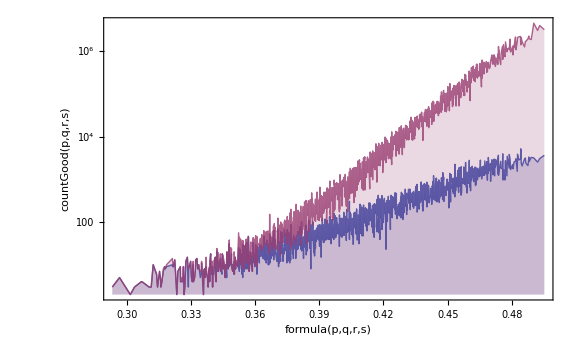

```mathematica
ListLogPlot[{formulaTable[myData[10]],formulaTable[myData[20]]}, 
			GridLines->{Join[Table[n,{n,0,0.6,0.01}],{{1/E,{Red, Thick}}}],Automatic},
                             PlotRange->All,
			LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
                              Ticks->{All,All,All},  
                              PerformanceGoal->"Quality", 
                              Method->"QuasiNewton",
                              ImageSize->Large,
                              PlotStyle->Opacity[0.8],
                              Joined->True,
                             Filling->Axis,
                             Frame->True,
			 AxesLabel->{"formula(p,q,r,s)","countGood(p,q,r,s)"}
                               ]
```

```mathematica
gr2500=formulaTableGraham[myData[2500]]
```

{{-0.226828,3},{-0.215395,5},{-0.198526,2},{-0.192038,3},{-0.181541,4},{-0.180588,4},{-0.169829,3},{-0.166653,3},{-0.163718,10},{-0.158623,6},{-0.157231,3},{-0.154213,7},{-0.152286,4},{-0.152226,3},{-0.15078,4},{-0.148613,8},{-0.146734,9},{-0.145798,8},{-0.143925,10},{-0.135301,14},{-0.135021,12},{-0.13391,9},{-0.131846,13},{-0.128929,2},{-0.127423,7},{-0.123816,9},{-0.123589,4},{-0.122478,5},{-0.120413,4},{-0.119406,9},{-0.118431,2},{-0.117419,3},{-0.116925,5},{-0.11599,12},{-0.113805,15},{-0.112383,8},{-0.111944,8},{-0.109118,12},{-0.107973,9},{-0.106719,4},{-0.105986,9},{-0.105493,12},{-0.105213,4},{-0.103544,5},{-0.102373,8},{-0.102038,13},{-0.100232,14},{-0.0991205,8},{-0.0991033,8},{-0.0976851,10},{-0.0970562,8},{-0.0955135,7},{-0.0940074,7},{-0.0937804,12},{-0.0911035,2},{-0.0906051,7},{-0.0897342,8},{-0.0895975,6},{-0.0891167,5},{-0.0890258,7},{-0.0886232,7},{-0.0876702,11},{-0.0876107,15},{-0.0865589,6},{-0.0855033,5},{-0.0846159,3},{-0.0839973,14},{-0.0826291,10},{-0.0825747,4},{-0.0822338,12},{-0.0821356,12},{-0.0811826,18},{-0.0808156,10},{-0.0793096,6},{-0.0790157,12},{-0.0785286,3},{-0.0781648,6},{-0.0769109,8},{-0.076178,13},{-0.0757462,11},{-0.0748467,15},{-0.074328,8},{-0.0741186,15},{-0.0737357,4},{-0.0725646,24},{-0.0721318,18},{-0.0708011,10},{-0.0706853,19},{-0.0704233,7},{-0.0685184,13},{-0.0678769,18},{-0.067248,9},{-0.0668163,7},{-0.0657053,12},{-0.0652489,23},{-0.0643135,16},{-0.0643132,13},{-0.0638307,10},{-0.063641,14},{-0.0624064,9},{-0.0612954,5},{-0.0604195,10},{-0.0599261,8},{-0.0593086,15},{-0.0592311,9},{-0.0592177,10},{-0.058973,22},{-0.0572443,8},{-0.0568061,23},{-0.0567508,14},{-0.0557978,38},{-0.0556951,22},{-0.0548078,12},{-0.0538163,25},{-0.0538159,10},{-0.0536308,13},{-0.0535366,19},{-0.0528805,40},{-0.0528209,13},{-0.0521184,8},{-0.0512007,7},{-0.0510074,10},{-0.0503613,9},{-0.0492139,6},{-0.0492075,20},{-0.0489431,10},{-0.0487204,10},{-0.0477674,19},{-0.0474441,8},{-0.0473283,13},{-0.0456004,16},{-0.0450385,10},{-0.044804,11},{-0.0445198,9},{-0.0443105,21},{-0.0433575,56},{-0.0423832,27},{-0.042331,17},{-0.0423237,44},{-0.042104,35},{-0.0421036,12},{-0.0413706,25},{-0.0411905,31},{-0.0409128,40},{-0.0392037,42},{-0.0389287,9},{-0.0389283,22},{-0.0387102,24},{-0.0379211,19},{-0.0377572,37},{-0.0370081,17},{-0.0369468,21},{-0.0365028,8},{-0.0359938,21},{-0.0359342,35},{-0.0358956,33},{-0.035616,11},{-0.034516,15},{-0.0340225,39},{-0.0338328,15},{-0.0330695,29},{-0.0325982,11},{-0.0324407,40},{-0.0323208,21},{-0.0309026,19},{-0.0308983,23},{-0.0308979,24},{-0.0306709,20},{-0.0306114,26},{-0.0304592,56},{-0.0295062,21},{-0.0294229,7},{-0.0276331,24},{-0.0274956,34},{-0.0274361,16},{-0.0269979,19},{-0.0264884,28},{-0.026488,17},{-0.0252345,7},{-0.0251187,47},{-0.0245016,43},{-0.0245012,15},{-0.0244103,23},{-0.0241833,65},{-0.0238226,20},{-0.0223102,28},{-0.0220592,18},{-0.0219434,40},{-0.0213925,14},{-0.021008,48},{-0.0208881,18},{-0.0208878,41},{-0.0200004,32},{-0.0194652,46},{-0.0194057,11},{-0.019135,14},{-0.0190261,32},{-0.0190089,43},{-0.0187469,24},{-0.0180136,37},{-0.0162004,49},{-0.0162001,32},{-0.0157923,27},{-0.0155716,32},{-0.0150553,39},{-0.0149958,41},{-0.0144001,40},{-0.0140288,32},{-0.013913,39},{-0.013686,66},{-0.0130685,51},{-0.0129776,43},{-0.0126367,61},{-0.0113824,24},{-0.0111046,49},{-0.0105107,63},{-0.0102311,52},{-0.00971246,50},{-0.00961892,53},{-0.00950311,49},{-0.00945508,39},{-0.00939554,49},{-0.00856771,46},{-0.00824961,67},{-0.00763211,57},{-0.00754122,42},{-0.0075163,55},{-0.00731384,107},{-0.0072966,29},{-0.00669466,39},{-0.0065809,58},{-0.00618561,140},{-0.00507432,62},{-0.00476739,39},{-0.00470785,31},{-0.00413855,39},{-0.00412131,68},{-0.00401868,50},{-0.00390286,50},{-0.00313131,48},{-0.00296747,152},{-0.00248034,28},{-0.00220073,65},{-0.00213943,43},{-0.00120404,268},{-0.0011445,57},{-0.00109442,44},{0.000302007,7546},{0.000669008,59},{0.000784825,41},{0.000974564,60},{0.00120157,57},{0.00172022,63},{0.00192957,82},{0.00220918,26},{0.00246893,110},{0.00295606,105},{0.00318344,119},{0.00389183,55},{0.00390907,51},{0.00391638,76},{0.00419599,36},{0.00434818,26},{0.00538447,28},{0.00635874,23},{0.00663797,63},{0.00715662,59},{0.00736597,71},{0.00737129,97},{0.00752981,124},{0.00780943,49},{0.00830174,41},{0.00831898,32},{0.00923195,85},{0.00929324,168},{0.00935278,115},{0.00957285,167},{0.00967106,112},{0.0102886,17},{0.0103058,74},{0.0107993,221},{0.0109847,100},{0.0122175,84},{0.0124072,61},{0.0124971,77},{0.0127481,144},{0.0128463,90},{0.0129662,80},{0.0134149,43},{0.0136419,33},{0.013902,55},{0.0139192,103},{0.0143891,61},{0.0146684,136},{0.0154017,68},{0.0156287,46},{0.0156724,103},{0.0157809,379},{0.0160605,334},{0.0168172,84},{0.0171715,787},{0.0176539,144},{0.0178436,59},{0.018071,59},{0.0185897,57},{0.0186069,52},{0.018799,107},{0.018804,87},{0.0190151,59},{0.0190783,61},{0.0192358,168},{0.0192421,126},{0.0198116,54},{0.0207785,200},{0.0207858,54},{0.0208767,51},{0.0210055,481},{0.0210651,182},{0.0222536,29},{0.0224174,163},{0.0225116,320},{0.023425,23},{0.0237028,199},{0.0239298,91},{0.0241808,101},{0.0242404,80},{0.0243993,73},{0.0245586,130},{0.0246785,156},{0.0248475,70},{0.0251884,143},{0.0252866,99},{0.0254118,93},{0.0256869,321},{0.0261014,54},{0.0265578,214},{0.0268343,61},{0.0271051,105},{0.0271753,255},{0.0272661,304},{0.0272735,117},{0.0274931,181},{0.0276687,409},{0.0278538,192},{0.0281127,81},{0.0286041,11546},{0.029087,173},{0.0292767,75},{0.0293662,125},{0.029733,210},{0.0300995,44},{0.0302839,260},{0.0304478,134},{0.0305113,67},{0.0306684,301},{0.0307887,103},{0.0308869,49},{0.0312443,135},{0.0316761,104},{0.0322112,177},{0.0322707,141},{0.0324981,62},{0.0325415,98},{0.032589,52},{0.0326503,520},{0.0336629,251},{0.0336866,61},{0.0337129,440},{0.0337173,1319},{0.0341564,658},{0.0348577,172},{0.0350559,87},{0.0351355,132},{0.0354764,369},{0.0355746,101},{0.0356734,49},{0.0357643,157},{0.0358842,237},{0.0361116,136},{0.0366211,121},{0.0366807,144},{0.0368445,132},{0.0369989,52},{0.0372763,175},{0.0377634,413},{0.0379904,464},{0.0381272,1069},{0.0386079,220},{0.0386988,160},{0.0389857,233},{0.0391014,836},{0.0392869,81},{0.039381,662},{0.0395454,131},{0.040114,986},{0.0401742,198},{0.0402941,159},{0.0405719,507},{0.0407992,225},{0.0411657,672},{0.0414453,171},{0.0415322,159},{0.041717,211},{0.041964,274},{0.042161,146},{0.0421733,188},{0.0422214,321},{0.0422809,374},{0.0425563,1692},{0.0425992,104},{0.0430863,390},{0.0431087,181},{0.0437038,215},{0.0437274,3119},{0.0439745,170},{0.0441601,889},{0.0443626,1956},{0.0449818,180},{0.0450955,357},{0.0451456,315},{0.045589,1335},{0.0457745,280},{0.0458686,1560},{0.0462616,135},{0.046909,290},{0.0469686,365},{0.0472869,85},{0.0473172,130},{0.0474962,124},{0.0475379,333},{0.0477736,912},{0.0481137,147},{0.0482046,194},{0.0484151,795},{0.048709,773},{0.0490439,2525},{0.0491961,755},{0.0494757,399},{0.049483,345},{0.0501914,86},{0.0504622,158},{0.050582,430},{0.0505867,1937},{0.0506715,253},{0.0508137,1830},{0.0517271,158},{0.0520049,191},{0.0524613,546},{0.052651,245},{0.0526583,185},{0.052878,168},{0.0530965,156},{0.0533967,296},{0.053606,191},{0.053714,342},{0.0538048,104},{0.0538856,508},{0.053989,1186},{0.0546013,159},{0.0548599,5196},{0.0549966,2898},{0.0555683,678},{0.0555928,337},{0.0558724,443},{0.0562717,225},{0.0563659,4636},{0.0564148,114},{0.0569834,3023},{0.0570609,460},{0.0570743,3902},{0.0573013,6479},{0.0577841,134},{0.0579739,214},{0.0580352,1775},{0.0582148,329},{0.0584016,217},{0.0584925,349},{0.0587019,379},{0.0590477,1706},{0.0592063,809},{0.0594859,331},{0.0595412,4708},{0.0599782,370},{0.0602016,166},{0.0604766,1919},{0.0605969,2586},{0.0606887,147},{0.0609084,494},{0.0609594,415},{0.0613475,2833},{0.0614842,4704},{0.061965,1183},{0.0620151,234},{0.0620194,664},{0.0623838,229},{0.0624585,3730},{0.0626612,919},{0.0629024,235},{0.0634115,7714728},{0.063471,13251},{0.0638939,838},{0.0640837,1944},{0.0641736,973},{0.0643021,184},{0.0643706,240},{0.0645228,2009},{0.0648893,205},{0.0650913,1346},{0.0650986,216},{0.0652846,1407},{0.0653183,804},{0.0655784,800},{0.0660656,733},{0.0664293,1359},{0.0670781,585},{0.0670845,7031},{0.0673051,364},{0.0673488,460},{0.0675716,7559},{0.0677986,9475},{0.067984,379},{0.0684161,2450},{0.0684936,838},{0.0685027,284},{0.068507,1766},{0.068712,230},{0.0689898,274},{0.0697475,1124},{0.0702661,909},{0.0704142,360},{0.0704755,225},{0.0704804,1298},{0.0706915,1164},{0.0706989,583},{0.0709185,912},{0.0709739,2669},{0.0712535,6006},{0.071488,673},{0.0717722,1709},{0.0719815,14247},{0.0720295,5102},{0.072401,424},{0.0724623,626},{0.0725532,1186},{0.0726717,394},{0.0729169,719},{0.0733997,465},{0.0735895,645},{0.0739088,9290},{0.0739683,8020},{0.0740938,494},{0.0741708,22236},{0.0749037,3484},{0.0751015,3408},{0.0753792,2113},{0.0753865,593},{0.0755763,176},{0.0756062,597},{0.0760144,365},{0.0760757,961},{0.0762351,742},{0.076524,1877},{0.0767172,3959},{0.0768109,342},{0.0769631,2045},{0.0770883,4296},{0.0773461,7149},{0.0775818,15800},{0.0777778,692},{0.0785108,823},{0.0785172,1727},{0.0787815,2886},{0.0789499,2686},{0.079,842},{0.0790043,743},{0.0791897,541},{0.0792839,28818},{0.0797891,725},{0.0799862,334},{0.0803964,17923},{0.0804243,413},{0.0807021,358},{0.0807634,2752},{0.0809531,1180},{0.0817759,3094},{0.0821242,1663},{0.0821878,173},{0.0822694,5352},{0.0824111,198},{0.0824592,40332},{0.0825633,6331},{0.0826862,1538},{0.0829207,2106},{0.0832048,3496},{0.0834142,3227},{0.0835996,939},{0.0836938,40656},{0.0838774,588},{0.0841746,915},{0.0842655,2899},{0.0846681,40189},{0.085112,351},{0.085363,237},{0.0853765,4656},{0.0853894,4552},{0.085401,5840},{0.0855864,566},{0.0856211,43946},{0.0856806,50294},{0.0865341,3584},{0.0867324,2185},{0.0868119,1717},{0.0868691,40011},{0.0870988,705},{0.087251,5327},{0.0873499,2516},{0.0874408,2676},{0.087788,1130},{0.0878434,3977},{0.0880166,770},{0.0882873,387},{0.0885209,6616},{0.0886754,1147},{0.0887964,5331},{0.0888559,98022},{0.0890144,4629},{0.089294,59490},{0.0897864,2883},{0.0902741,235},{0.0906622,890},{0.0907123,665},{0.0907166,4352},{0.0909633,1995},{0.0911557,59192},{0.0912218,3676},{0.09163,923},{0.0917732,5417},{0.0918507,1983},{0.0921087,38443},{0.0924693,67291},{0.0924757,2036},{0.0932086,2941},{0.0933934,957},{0.0936168,925},{0.0937021,4944},{0.0938375,4370},{0.0938876,357},{0.0938919,9656},{0.0939817,10862},{0.0942756,2432},{0.094331,7954},{0.0947627,2832},{0.0948995,71153},{0.0951265,11543},{0.095284,12347},{0.0953802,2816},{0.0953866,8489},{0.095651,1233},{0.0958737,9565},{0.0963177,1053},{0.0968221,3101},{0.0968267,6458},{0.0968863,107766},{0.0971133,8976},{0.097157,8722},{0.0972659,46584},{0.0974509,9604},{0.097938,8958},{0.0980267,1305},{0.0983018,3831},{0.0983045,1818},{0.0989633,1868},{0.0989937,8781},{0.0991727,6239},{0.0995556,10114},{0.0997902,2379},{0.099881,1264},{0.100074,11490},{0.100284,9353},{0.100289,10538},{0.1005,162740},{0.100727,14752},{0.101159,3828},{0.101237,1277},{0.101296,129981},{0.101868,4126},{0.101918,764},{0.102139,2899},{0.10227,12961},{0.102348,18407},{0.102361,15768},{0.102606,165714},{0.102714,1519},{0.103223,895},{0.103314,14632},{0.103404,1086},{0.103681,8162},{0.103902,18768},{0.104335,16019},{0.104773,6527},{0.10491,210464},{0.105187,32789},{0.10539,3203},{0.105414,18702},{0.105481,5732},{0.105781,11781},{0.105884,8996},{0.106043,15833},{0.106278,26730},{0.106328,1307},{0.106332,11283},{0.106771,18272},{0.106837,1525},{0.106896,18598},{0.107586,22433},{0.107724,1699},{0.107948,34243},{0.108091,12041},{0.108315,1028},{0.108319,14029},{0.10859,17801},{0.108699,167928},{0.108758,14839},{0.108978,69334},{0.109461,18463},{0.109597,19593},{0.10965,13208},{0.109711,558},{0.109891,14467},{0.110078,15306},{0.110169,6539},{0.110378,3796},{0.110572,17737},{0.110761,30061},{0.111525,3387},{0.111584,20268},{0.111878,18671},{0.111932,26957},{0.111996,33352},{0.112153,37040},{0.112365,18589},{0.112372,11462},{0.112636,23208},{0.112729,36211},{0.113325,1120},{0.113692,14593},{0.113812,13177},{0.113983,18402},{0.11406,25410},{0.114074,15770},{0.114579,15349},{0.115171,34061},{0.115198,14586},{0.115979,23620},{0.116047,4223},{0.116342,21807},{0.116541,23623},{0.116566,15374},{0.11662,15446},{0.116775,15083},{0.117059,31746},{0.117158,43457},{0.117249,63339},{0.117494,45696},{0.117596,42814},{0.118012,2519},{0.118222,2037},{0.118329,51327},{0.118484,29164},{0.119475,526086},{0.11966,8927},{0.120179,22526},{0.120184,59548},{0.120208,3060},{0.120388,42287},{0.120411,743370},{0.12047,28160},{0.120666,89362},{0.120771,20021},{0.12103,43429},{0.121659,43047},{0.122091,24974},{0.122284,63449},{0.122375,17841},{0.122651,50324},{0.123017,49083},{0.123202,62010},{0.123586,3770},{0.123646,52663},{0.123822,2921},{0.124077,19084},{0.124084,24383},{0.124348,34069},{0.124571,19701},{0.124594,3169},{0.125076,45951},{0.125188,52223},{0.125266,19394},{0.125459,64237},{0.125524,38162},{0.125963,1929343},{0.126581,5995},{0.12663,76762},{0.127063,81273},{0.127253,7368},{0.127259,71671},{0.127691,25762},{0.127746,61032},{0.128487,10111},{0.128509,3627},{0.128699,66495},{0.128771,47982},{0.128802,28788},{0.128981,108152},{0.129138,118730},{0.129598,42193},{0.129689,29732},{0.129934,2862},{0.130194,4277},{0.130676,149666},{0.130681,51939},{0.130866,11341},{0.130908,1071153},{0.130968,52912},{0.131616,3818},{0.131663,13873},{0.131676,166765},{0.131921,6195},{0.131947,120599},{0.132101,30217},{0.132156,116830},{0.132379,60993},{0.133109,4671},{0.133212,39240},{0.13349,65850},{0.134083,3913},{0.134088,53555},{0.134143,72211},{0.134363,141592},{0.134581,179047},{0.134882,4619},{0.135091,9169},{0.135096,3170},{0.135199,98309},{0.135276,97767},{0.135289,55475},{0.135534,4130},{0.135554,38733},{0.136026,4169},{0.136086,103126},{0.136788,21395},{0.137078,8187},{0.137169,239040},{0.137263,67112},{0.137396,116656},{0.137756,105442},{0.137899,115081},{0.138013,3049},{0.138709,5013},{0.138775,26420},{0.139269,192415},{0.139459,155520},{0.139693,6521},{0.139699,72392},{0.139886,118861},{0.139964,39920},{0.139977,137621},{0.140187,98641},{0.140222,5123},{0.140571,8823},{0.140691,9869},{0.140851,160151},{0.14114,5984},{0.141579,2219},{0.141627,12979},{0.141686,160385},{0.141951,33325},{0.142114,4954},{0.142173,101843},{0.142389,113713},{0.142393,73760},{0.142444,177320},{0.143126,4917},{0.143306,34443},{0.143397,6584},{0.1435,142553},{0.143565,6325},{0.143868,59509},{0.144387,123968},{0.145293,91223},{0.145379,11186},{0.145564,88106},{0.145569,246619},{0.145787,126739},{0.145796,7691},{0.145855,122698},{0.146314,13368},{0.146374,126765},{0.146524,10889},{0.146583,183403},{0.14674,8091},{0.146803,7615},{0.147179,5013},{0.147536,8067},{0.147994,126904},{0.14851,4725},{0.148601,10473},{0.14879,6062},{0.148881,301586},{0.149469,109829},{0.149703,166213},{0.149979,6985},{0.149981,175290},{0.149987,216070},{0.150197,237308},{0.150474,277983},{0.15115,8354},{0.151348,322238},{0.151427,14833},{0.151867,5655},{0.151899,275543},{0.151965,8619},{0.152056,549134},{0.152124,17925},{0.152183,295496},{0.152283,15774},{0.152404,10092},{0.153011,10214},{0.153136,5046},{0.153291,3805},{0.153594,307482},{0.153826,14000},{0.153886,346677},{0.154156,280817},{0.154265,486833},{0.154391,86802},{0.154884,515082},{0.154998,6886},{0.155074,473908},{0.155278,5518},{0.155579,5712},{0.155837,11500},{0.156466,13435},{0.156812,18428},{0.156871,450924},{0.157001,16141},{0.157061,667652},{0.157091,12103},{0.15744,18060},{0.157499,183026},{0.157824,11307},{0.158004,240216},{0.158009,12967},{0.158236,10766},{0.158296,567100},{0.158453,8904},{0.158612,16974},{0.158891,10206},{0.159378,710027},{0.159991,610545},{0.159996,8428},{0.160223,11904},{0.160267,14593},{0.160314,8674},{0.160485,562415},{0.160674,410353},{0.161411,13220},{0.161438,16033},{0.161471,335103},{0.161909,385736},{0.162066,12673},{0.162187,586562},{0.162554,681477},{0.162781,18564},{0.163299,23004},{0.163398,19795},{0.163489,22309},{0.163579,8517},{0.163609,8663},{0.163788,24417},{0.163836,23468},{0.163896,651550},{0.164406,14731},{0.164497,8323},{0.164724,14356},{0.165084,613048},{0.165362,981363},{0.165471,14332},{0.165775,21577},{0.166483,8858},{0.166597,787602},{0.16671,12025},{0.166754,14795},{0.166963,28182},{0.167012,23244},{0.167071,584780},{0.167899,22794},{0.168019,20946},{0.168297,28380},{0.168524,26324},{0.168583,1025471},{0.16895,19120},{0.169153,17272},{0.169388,30483},{0.169442,25446},{0.169501,1172260},{0.169772,876565},{0.169881,20046},{0.169886,17179},{0.170006,19346},{0.170097,18788},{0.170324,22964},{0.170811,23093},{0.170893,14899},{0.171428,22304},{0.171699,26373},{0.171759,1094339},{0.171868,32003},{0.172197,1347952},{0.172564,33882},{0.172707,30993},{0.173115,613001},{0.173499,31944},{0.173986,27924},{0.174076,37628},{0.174266,1227815},{0.174507,19715},{0.174694,19082},{0.174785,17914},{0.174994,29810},{0.175012,17422},{0.175042,27705},{0.175101,292998},{0.175221,18656},{0.175372,851288},{0.175481,25170},{0.175838,25995},{0.175929,24517},{0.176494,24901},{0.176981,23450},{0.177183,37050},{0.177208,22853},{0.177251,35290},{0.177802,1773008},{0.177916,30258},{0.178187,43458},{0.178307,32508},{0.178396,22203},{0.178676,38945},{0.179194,29889},{0.179452,41752},{0.179511,36623},{0.17965,17624},{0.17973,41690},{0.179789,39408},{0.180169,41805},{0.180358,36451},{0.180383,27834},{0.180594,21558},{0.180663,31293},{0.180821,33592},{0.181181,23567},{0.181391,46863},{0.181439,17329},{0.18153,50334},{0.181593,16202},{0.182326,26937},{0.183403,40328},{0.18358,31597},{0.183996,28376},{0.184139,35852},{0.184199,39795},{0.184276,31567},{0.184768,33695},{0.184795,19409},{0.185004,50732},{0.185282,62540},{0.185509,49622},{0.185699,26994},{0.185939,65887},{0.186126,22675},{0.186138,59978},{0.186217,67691},{0.186427,39601},{0.186706,36067},{0.186755,65370},{0.186991,23019},{0.187193,53879},{0.18768,36936},{0.187812,36911},{0.187926,36332},{0.188413,34840},{0.188684,45067},{0.188693,36539},{0.188964,57482},{0.189692,48655},{0.18974,57829},{0.189799,36890},{0.189881,49818},{0.190108,51696},{0.190369,65131},{0.190627,67431},{0.190856,35112},{0.191679,59798},{0.191868,31039},{0.191881,65478},{0.192027,34257},{0.19209,37673},{0.192095,53821},{0.192306,56983},{0.192614,43458},{0.192799,39636},{0.192823,35956},{0.193103,52437},{0.194077,71850},{0.194168,88933},{0.194786,37290},{0.195056,112068},{0.195266,52660},{0.195292,45707},{0.195482,41607},{0.195709,59322},{0.196227,85635},{0.196278,69602},{0.196437,89753},{0.196714,61741},{0.196716,64846},{0.196994,100810},{0.197252,121611},{0.197343,79614},{0.197691,83149},{0.198139,66512},{0.198399,69670},{0.198424,39675},{0.198578,104339},{0.198703,53214},{0.199195,58324},{0.199892,60529},{0.200126,38222},{0.200169,101550},{0.200396,41274},{0.200565,105292},{0.200866,52008},{0.201124,91106},{0.201314,100478},{0.201404,88778},{0.201753,149122},{0.201878,59460},{0.202378,107422},{0.202568,69889},{0.202809,54375},{0.203087,118508},{0.203111,71144},{0.203296,82027},{0.203301,40470},{0.203391,85330},{0.203739,124170},{0.20374,176578},{0.204178,91798},{0.204309,71532},{0.204536,91033},{0.204579,87361},{0.204796,113687},{0.205283,116297},{0.205554,118262},{0.206566,50458},{0.206725,89229},{0.206914,124155},{0.206978,55474},{0.207004,137086},{0.207353,138254},{0.207497,104466},{0.207711,95894},{0.207922,95668},{0.208149,159173},{0.208427,100143},{0.208866,115478},{0.208896,107581},{0.208965,96735},{0.209056,138303},{0.209483,104451},{0.209693,76567},{0.209784,154898},{0.209909,69727},{0.210136,117809},{0.21018,52240},{0.211324,163677},{0.211602,98895},{0.21177,136438},{0.212041,174913},{0.212578,101625},{0.21261,158852},{0.212837,101453},{0.213097,187327},{0.213306,140900},{0.213311,52445},{0.213466,190332},{0.213584,189759},{0.214319,84454},{0.214596,88525},{0.214823,112720},{0.215008,82045},{0.215293,144209},{0.215384,163773},{0.215452,176960},{0.215741,177992},{0.216012,187240},{0.21618,221323},{0.216995,115351},{0.217266,132057},{0.217994,201069},{0.217999,92482},{0.218184,151532},{0.21821,211229},{0.218437,130968},{0.219006,92108},{0.219066,288280},{0.219355,226927},{0.219553,236182},{0.219794,163375},{0.219981,281301},{0.220072,253410},{0.22017,169770},{0.220609,213192},{0.221341,176188},{0.221405,188883},{0.221496,194563},{0.221612,111454},{0.221781,165686},{0.22262,142974},{0.223483,175143},{0.223594,346366},{0.223753,250257},{0.223784,149302},{0.223963,243729},{0.224042,303489},{0.224481,316823},{0.22458,246850},{0.224607,69899},{0.224671,287907},{0.225018,183832},{0.225296,293701},{0.225751,184275},{0.22595,418814},{0.226029,229014},{0.226468,295500},{0.226658,255584},{0.227005,270538},{0.227096,421085},{0.227893,451092},{0.228194,210458},{0.228472,375464},{0.229563,314506},{0.229643,268012},{0.229706,193915},{0.230082,294763},{0.230181,254356},{0.230271,410476},{0.230439,285096},{0.231068,498399},{0.231506,285813},{0.231693,249891},{0.231784,498591},{0.231993,236471},{0.232611,315389},{0.232881,328306},{0.233493,261413},{0.23398,377171},{0.234053,455819},{0.234251,504517},{0.234681,519833},{0.234868,367677},{0.234959,433412},{0.235168,266498},{0.235306,394480},{0.236039,147432},{0.236194,446011},{0.236224,227207},{0.236668,626305},{0.237155,337892},{0.237593,345128},{0.238181,354886},{0.238211,357297},{0.23839,557412},{0.238482,294618},{0.239098,449309},{0.239369,521670},{0.240769,416861},{0.240912,578400},{0.241356,319705},{0.241565,538461},{0.241794,502474},{0.242003,339833},{0.242281,537085},{0.242621,435158},{0.242712,518732},{0.242899,551961},{0.24399,395437},{0.244699,427142},{0.244969,557116},{0.245179,608254},{0.245456,634377},{0.246512,823443},{0.246691,591120},{0.246881,574982},{0.247165,501173},{0.247309,619279},{0.247399,715679},{0.248678,831436},{0.248868,496967},{0.249108,766270},{0.249386,508341},{0.249596,692826},{0.249866,446417},{0.250922,563238},{0.251853,721214},{0.252291,495274},{0.252481,872107},{0.252909,694920},{0.253,1300317},{0.253209,755831},{0.253277,1067515},{0.253796,739470},{0.255196,488918},{0.255467,845103},{0.256891,1310820},{0.257169,648258},{0.25741,810183},{0.257897,1439530},{0.258878,808442},{0.259396,748834},{0.259606,928437},{0.259884,1666933},{0.261308,977948},{0.261579,1131432},{0.263497,1188963},{0.263565,1096631},{0.264293,1928608},{0.264483,1107737},{0.264921,964543},{0.266908,1323575},{0.267179,826168},{0.267907,1325057},{0.268097,1228400},{0.269609,2170035},{0.269894,1489059},{0.270083,1090124},{0.271318,1663572},{0.271596,2102103},{0.272784,2187606},{0.274493,2232617},{0.274771,1422075},{0.275209,2105111},{0.276006,1694249},{0.278385,1271006},{0.279181,1708525},{0.279619,1713166},{0.281606,1961456},{0.282524,2282074},{0.282794,1970988},{0.284781,1888291},{0.287211,4572608},{0.290825,3095411},{0.292812,4023872},{0.297222,3215978}}

```mathematica
gr20=formulaTableGraham[myData[20]]
```

{{-0.226828,3},{-0.215395,5},{-0.198526,2},{-0.192038,3},{-0.181541,4},{-0.180588,4},{-0.169829,3},{-0.166653,3},{-0.163718,10},{-0.158623,6},{-0.157231,3},{-0.154213,7},{-0.152286,4},{-0.152226,3},{-0.15078,4},{-0.148613,8},{-0.146734,9},{-0.145798,8},{-0.143925,10},{-0.135301,14},{-0.135021,12},{-0.13391,9},{-0.131846,13},{-0.128929,2},{-0.127423,7},{-0.123816,9},{-0.123589,4},{-0.122478,5},{-0.120413,4},{-0.119406,9},{-0.118431,2},{-0.117419,3},{-0.116925,5},{-0.11599,12},{-0.113805,15},{-0.112383,8},{-0.111944,8},{-0.109118,12},{-0.107973,5},{-0.106719,4},{-0.105986,9},{-0.105493,12},{-0.105213,4},{-0.103544,5},{-0.102373,8},{-0.102038,13},{-0.100232,14},{-0.0991205,8},{-0.0991033,8},{-0.0976851,10},{-0.0970562,8},{-0.0955135,7},{-0.0940074,7},{-0.0937804,12},{-0.0911035,2},{-0.0906051,7},{-0.0897342,8},{-0.0895975,6},{-0.0891167,5},{-0.0890258,6},{-0.0886232,7},{-0.0876702,11},{-0.0876107,15},{-0.0865589,6},{-0.0855033,5},{-0.0846159,3},{-0.0839973,7},{-0.0826291,9},{-0.0825747,4},{-0.0822338,12},{-0.0821356,12},{-0.0811826,18},{-0.0808156,10},{-0.0793096,6},{-0.0790157,12},{-0.0785286,3},{-0.0781648,6},{-0.0769109,8},{-0.076178,13},{-0.0757462,11},{-0.0748467,15},{-0.074328,5},{-0.0741186,15},{-0.0737357,4},{-0.0725646,24},{-0.0721318,18},{-0.0708011,10},{-0.0706853,19},{-0.0704233,7},{-0.0685184,12},{-0.0678769,18},{-0.067248,9},{-0.0668163,7},{-0.0657053,12},{-0.0652489,18},{-0.0643135,16},{-0.0643132,13},{-0.0638307,8},{-0.063641,14},{-0.0624064,9},{-0.0612954,5},{-0.0604195,10},{-0.0599261,8},{-0.0593086,15},{-0.0592311,9},{-0.0592177,10},{-0.058973,20},{-0.0572443,8},{-0.0568061,16},{-0.0567508,14},{-0.0557978,38},{-0.0556951,22},{-0.0548078,11},{-0.0538163,25},{-0.0538159,10},{-0.0536308,13},{-0.0535366,19},{-0.0528805,24},{-0.0528209,13},{-0.0521184,8},{-0.0512007,7},{-0.0510074,10},{-0.0503613,9},{-0.0492139,6},{-0.0492075,20},{-0.0489431,10},{-0.0487204,10},{-0.0477674,15},{-0.0474441,8},{-0.0473283,13},{-0.0456004,12},{-0.0450385,10},{-0.044804,11},{-0.0445198,9},{-0.0443105,19},{-0.0433575,56},{-0.0423832,20},{-0.042331,17},{-0.0423237,44},{-0.042104,12},{-0.0421036,12},{-0.0413706,25},{-0.0411905,11},{-0.0409128,40},{-0.0392037,32},{-0.0389287,9},{-0.0389283,22},{-0.0387102,21},{-0.0379211,8},{-0.0377572,37},{-0.0370081,16},{-0.0369468,9},{-0.0365028,8},{-0.0359938,15},{-0.0359342,16},{-0.0358956,28},{-0.035616,11},{-0.034516,15},{-0.0340225,39},{-0.0338328,15},{-0.0330695,29},{-0.0325982,11},{-0.0324407,40},{-0.0323208,21},{-0.0309026,17},{-0.0308983,23},{-0.0308979,24},{-0.0306709,11},{-0.0306114,26},{-0.0304592,46},{-0.0295062,10},{-0.0294229,7},{-0.0276331,24},{-0.0274956,34},{-0.0274361,14},{-0.0269979,19},{-0.0264884,16},{-0.026488,17},{-0.0252345,7},{-0.0251187,36},{-0.0245016,40},{-0.0245012,15},{-0.0244103,23},{-0.0241833,43},{-0.0238226,20},{-0.0223102,28},{-0.0220592,10},{-0.0219434,40},{-0.0213925,14},{-0.021008,48},{-0.0208881,18},{-0.0208878,41},{-0.0200004,19},{-0.0194652,46},{-0.0194057,9},{-0.019135,14},{-0.0190261,31},{-0.0190089,43},{-0.0187469,24},{-0.0180136,31},{-0.0162004,29},{-0.0162001,32},{-0.0157923,27},{-0.0155716,29},{-0.0150553,39},{-0.0149958,41},{-0.0144001,21},{-0.0140288,32},{-0.013913,25},{-0.013686,37},{-0.0130685,51},{-0.0129776,43},{-0.0126367,46},{-0.0113824,24},{-0.0111046,26},{-0.0105107,63},{-0.0102311,52},{-0.00971246,47},{-0.00961892,53},{-0.00950311,49},{-0.00945508,32},{-0.00939554,49},{-0.00856771,33},{-0.00824961,30},{-0.00763211,53},{-0.00754122,34},{-0.0075163,55},{-0.00731384,60},{-0.0072966,29},{-0.00669466,39},{-0.0065809,52},{-0.00618561,56},{-0.00507432,62},{-0.00476739,39},{-0.00470785,25},{-0.00413855,39},{-0.00412131,18},{-0.00401868,26},{-0.00390286,50},{-0.00313131,42},{-0.00296747,152},{-0.00248034,28},{-0.00220073,49},{-0.00213943,43},{-0.00120404,44},{-0.0011445,33},{-0.00109442,44},{0.000302007,22},{0.000669008,59},{0.000784825,41},{0.000974564,60},{0.00120157,36},{0.00172022,63},{0.00192957,82},{0.00220918,26},{0.00246893,64},{0.00295606,92},{0.00318344,32},{0.00389183,55},{0.00390907,51},{0.00391638,76},{0.00419599,36},{0.00434818,23},{0.00538447,28},{0.00635874,23},{0.00663797,63},{0.00715662,59},{0.00736597,71},{0.00737129,97},{0.00752981,124},{0.00780943,49},{0.00830174,41},{0.00831898,32},{0.00923195,85},{0.00929324,67},{0.00935278,48},{0.00957285,49},{0.00967106,50},{0.0102886,17},{0.0103058,71},{0.0107993,25},{0.0109847,100},{0.0122175,84},{0.0124072,61},{0.0124971,77},{0.0127481,34},{0.0128463,90},{0.0129662,80},{0.0134149,43},{0.0136419,33},{0.013902,55},{0.0139192,45},{0.0143891,33},{0.0146684,76},{0.0154017,68},{0.0156287,46},{0.0156724,103},{0.0157809,81},{0.0160605,111},{0.0168172,84},{0.0171715,103},{0.0176539,49},{0.0178436,59},{0.018071,59},{0.0185897,57},{0.0186069,52},{0.018799,107},{0.018804,87},{0.0190151,59},{0.0190783,31},{0.0192358,135},{0.0192421,126},{0.0198116,54},{0.0207785,107},{0.0207858,54},{0.0208767,51},{0.0210055,110},{0.0210651,54},{0.0222536,29},{0.0224174,163},{0.0225116,64},{0.023425,23},{0.0237028,199},{0.0239298,91},{0.0241808,101},{0.0242404,63},{0.0243993,73},{0.0245586,130},{0.0246785,52},{0.0248475,70},{0.0251884,36},{0.0252866,99},{0.0254118,93},{0.0256869,30},{0.0261014,54},{0.0265578,78},{0.0268343,61},{0.0271051,105},{0.0271753,54},{0.0272661,101},{0.0272735,117},{0.0274931,39},{0.0276687,175},{0.0278538,93},{0.0281127,81},{0.0286041,76},{0.029087,173},{0.0292767,75},{0.0293662,112},{0.029733,82},{0.0300995,30},{0.0302839,260},{0.0304478,134},{0.0305113,67},{0.0306684,147},{0.0307887,57},{0.0308869,49},{0.0312443,135},{0.0316761,87},{0.0322112,88},{0.0322707,128},{0.0324981,62},{0.0325415,98},{0.032589,52},{0.0326503,189},{0.0336629,102},{0.0336866,61},{0.0337129,62},{0.0337173,136},{0.0341564,54},{0.0348577,172},{0.0350559,87},{0.0351355,132},{0.0354764,88},{0.0355746,101},{0.0356734,49},{0.0357643,157},{0.0358842,237},{0.0361116,136},{0.0366211,121},{0.0366807,29},{0.0368445,132},{0.0369989,52},{0.0372763,59},{0.0377634,91},{0.0379904,155},{0.0381272,131},{0.0386079,104},{0.0386988,160},{0.0389857,233},{0.0391014,127},{0.0392869,81},{0.039381,199},{0.0395454,131},{0.040114,143},{0.0401742,198},{0.0402941,66},{0.0405719,297},{0.0407992,225},{0.0411657,178},{0.0414453,132},{0.0415322,159},{0.041717,211},{0.041964,83},{0.042161,146},{0.0421733,44},{0.0422214,321},{0.0422809,145},{0.0425563,117},{0.0425992,104},{0.0430863,31},{0.0431087,181},{0.0437038,215},{0.0437274,226},{0.0439745,170},{0.0441601,192},{0.0443626,271},{0.0449818,180},{0.0450955,139},{0.0451456,315},{0.045589,285},{0.0457745,280},{0.0458686,59},{0.0462616,135},{0.046909,129},{0.0469686,269},{0.0472869,85},{0.0473172,130},{0.0474962,124},{0.0475379,333},{0.0477736,124},{0.0481137,147},{0.0482046,194},{0.0484151,144},{0.048709,269},{0.0490439,152},{0.0491961,483},{0.0494757,158},{0.049483,345},{0.0501914,86},{0.0504622,158},{0.050582,272},{0.0505867,131},{0.0506715,253},{0.0508137,222},{0.0517271,158},{0.0520049,191},{0.0524613,161},{0.052651,179},{0.0526583,185},{0.052878,111},{0.0530965,156},{0.0533967,241},{0.053606,191},{0.053714,342},{0.0538048,104},{0.0538856,159},{0.053989,270},{0.0546013,159},{0.0548599,302},{0.0549966,335},{0.0555683,504},{0.0555928,337},{0.0558724,153},{0.0562717,225},{0.0563659,330},{0.0564148,114},{0.0569834,235},{0.0570609,122},{0.0570743,128},{0.0573013,202},{0.0577841,134},{0.0579739,214},{0.0580352,108},{0.0582148,329},{0.0584016,217},{0.0584925,349},{0.0587019,379},{0.0590477,315},{0.0592063,654},{0.0594859,197},{0.0595412,218},{0.0599782,244},{0.0602016,166},{0.0604766,128},{0.0605969,329},{0.0606887,147},{0.0609084,348},{0.0609594,415},{0.0613475,392},{0.0614842,108},{0.061965,381},{0.0620151,234},{0.0620194,291},{0.0623838,229},{0.0624585,300},{0.0626612,245},{0.0629024,235},{0.0634115,397},{0.063471,161},{0.0638939,502},{0.0640837,222},{0.0641736,266},{0.0643021,184},{0.0643706,240},{0.0645228,332},{0.0648893,205},{0.0650913,377},{0.0650986,216},{0.0652846,277},{0.0653183,263},{0.0655784,502},{0.0660656,263},{0.0664293,341},{0.0670781,374},{0.0670845,94},{0.0673051,364},{0.0673488,436},{0.0675716,324},{0.0677986,633},{0.067984,379},{0.0684161,216},{0.0684936,603},{0.0685027,284},{0.068507,223},{0.068712,230},{0.0689898,274},{0.0697475,325},{0.0702661,565},{0.0704142,360},{0.0704755,225},{0.0704804,541},{0.0706915,432},{0.0706989,583},{0.0709185,912},{0.0709739,344},{0.0712535,153},{0.071488,182},{0.0717722,126},{0.0719815,531},{0.0720295,332},{0.072401,424},{0.0724623,596},{0.0725532,353},{0.0726717,394},{0.0729169,399},{0.0733997,465},{0.0735895,645},{0.0739088,305},{0.0739683,523},{0.0740938,494},{0.0741708,474},{0.0749037,112},{0.0751015,514},{0.0753792,623},{0.0753865,593},{0.0755763,176},{0.0756062,597},{0.0760144,365},{0.0760757,961},{0.0762351,742},{0.076524,792},{0.0767172,195},{0.0768109,342},{0.0769631,402},{0.0770883,434},{0.0773461,390},{0.0775818,567},{0.0777778,579},{0.0785108,823},{0.0785172,516},{0.0787815,440},{0.0789499,560},{0.079,842},{0.0790043,706},{0.0791897,541},{0.0792839,484},{0.0797891,442},{0.0799862,334},{0.0803964,403},{0.0804243,413},{0.0807021,358},{0.0807634,562},{0.0809531,794},{0.0817759,569},{0.0821242,417},{0.0821878,173},{0.0822694,764},{0.0824111,198},{0.0824592,292},{0.0825633,703},{0.0826862,647},{0.0829207,1290},{0.0832048,418},{0.0834142,767},{0.0835996,939},{0.0836938,454},{0.0838774,588},{0.0841746,769},{0.0842655,613},{0.0846681,688},{0.085112,351},{0.085363,237},{0.0853765,423},{0.0853894,614},{0.085401,912},{0.0855864,566},{0.0856211,828},{0.0856806,764},{0.0865341,982},{0.0867324,793},{0.0868119,930},{0.0868691,686},{0.0870988,705},{0.087251,1086},{0.0873499,848},{0.0874408,677},{0.087788,1130},{0.0878434,797},{0.0880166,770},{0.0882873,387},{0.0885209,1103},{0.0886754,850},{0.0887964,556},{0.0888559,752},{0.0890144,1313},{0.089294,749},{0.0897864,360},{0.0902741,235},{0.0906622,890},{0.0907123,665},{0.0907166,614},{0.0909633,647},{0.0911557,831},{0.0912218,727},{0.09163,923},{0.0917732,176},{0.0918507,1141},{0.0921087,345},{0.0924693,888},{0.0924757,1039},{0.0932086,776},{0.0933934,957},{0.0936168,925},{0.0937021,964},{0.0938375,1501},{0.0938876,357},{0.0938919,680},{0.0939817,749},{0.0942756,1135},{0.094331,975},{0.0947627,1248},{0.0948995,1819},{0.0951265,1316},{0.095284,916},{0.0953802,1641},{0.0953866,467},{0.095651,1005},{0.0958737,1035},{0.0963177,1053},{0.0968221,1265},{0.0968267,1158},{0.0968863,934},{0.0971133,480},{0.097157,821},{0.0972659,528},{0.0974509,1755},{0.097938,685},{0.0980267,1305},{0.0983018,1470},{0.0983045,1818},{0.0989633,1868},{0.0989937,1653},{0.0991727,287},{0.0995556,541},{0.0997902,910},{0.099881,1264},{0.100074,386},{0.100284,1101},{0.100289,1136},{0.1005,1888},{0.100727,1082},{0.101159,937},{0.101237,1277},{0.101296,1917},{0.101868,1359},{0.101918,764},{0.102139,1784},{0.10227,1510},{0.102348,551},{0.102361,963},{0.102606,638},{0.102714,1519},{0.103223,895},{0.103314,1131},{0.103404,998},{0.103681,2701},{0.103902,767},{0.104335,1333},{0.104773,881},{0.10491,2239},{0.105187,2221},{0.10539,2867},{0.105414,1004},{0.105481,2014},{0.105781,1664},{0.105884,2385},{0.106043,1359},{0.106278,1503},{0.106328,1307},{0.106332,1947},{0.106771,1583},{0.106837,1525},{0.106896,1006},{0.107586,1157},{0.107724,1699},{0.107948,917},{0.108091,1652},{0.108315,1028},{0.108319,615},{0.10859,1024},{0.108699,2560},{0.108758,1507},{0.108978,899},{0.109461,2360},{0.109597,1697},{0.10965,2358},{0.109711,558},{0.109891,2203},{0.110078,3178},{0.110169,2645},{0.110378,2837},{0.110572,3214},{0.110761,2530},{0.111525,3387},{0.111584,564},{0.111878,2121},{0.111932,2424},{0.111996,1830},{0.112153,2244},{0.112365,2414},{0.112372,1258},{0.112636,2570},{0.112729,1577},{0.113325,1120},{0.113692,1876},{0.113812,2478},{0.113983,1867},{0.11406,2765},{0.114074,2926},{0.114579,3345},{0.115171,2020},{0.115198,1447},{0.115979,1567},{0.116047,2992},{0.116342,2617},{0.116541,1930},{0.116566,1267},{0.11662,1081},{0.116775,1037},{0.117059,602},{0.117158,2740},{0.117249,1893},{0.117494,1794},{0.117596,4390},{0.118012,2519},{0.118222,2037},{0.118329,1155},{0.118484,2637},{0.119475,2534},{0.11966,4107},{0.120179,3793},{0.120184,2027},{0.120208,3060},{0.120388,985},{0.120411,4643},{0.12047,2262},{0.120666,2953},{0.120771,1930},{0.12103,2813},{0.121659,3573},{0.122091,2574},{0.122284,4241},{0.122375,2849},{0.122651,2718},{0.123017,1682},{0.123202,2369},{0.123586,3462},{0.123646,3956},{0.123822,2921},{0.124077,6811},{0.124084,3728},{0.124348,4822},{0.124571,4642},{0.124594,3169},{0.125076,863},{0.125188,1828},{0.125266,5323},{0.125459,3016},{0.125524,2409},{0.125963,2265},{0.126581,5995},{0.12663,2120},{0.127063,3954},{0.127253,6976},{0.127259,4791},{0.127691,3245},{0.127746,2921},{0.128487,5141},{0.128509,3627},{0.128699,4187},{0.128771,3564},{0.128802,2080},{0.128981,2643},{0.129138,4752},{0.129598,6308},{0.129689,4283},{0.129934,2862},{0.130194,4277},{0.130676,3873},{0.130681,3821},{0.130866,2922},{0.130908,5868},{0.130968,7372},{0.131616,3818},{0.131663,5661},{0.131676,1446},{0.131921,6195},{0.131947,1998},{0.132101,3959},{0.132156,5174},{0.132379,6604},{0.133109,4671},{0.133212,2836},{0.13349,6674},{0.134083,3913},{0.134088,6879},{0.134143,9800},{0.134363,3379},{0.134581,6025},{0.134882,4619},{0.135091,9169},{0.135096,3170},{0.135199,4748},{0.135276,4516},{0.135289,2483},{0.135534,4130},{0.135554,5563},{0.136026,4169},{0.136086,5144},{0.136788,8184},{0.137078,8187},{0.137169,3695},{0.137263,7228},{0.137396,4030},{0.137756,5348},{0.137899,4355},{0.138013,3049},{0.138709,5013},{0.138775,6635},{0.139269,6819},{0.139459,4073},{0.139693,6521},{0.139699,5706},{0.139886,6880},{0.139964,6522},{0.139977,4033},{0.140187,3033},{0.140222,5123},{0.140571,8823},{0.140691,9869},{0.140851,3848},{0.14114,5984},{0.141579,2219},{0.141627,12979},{0.141686,4967},{0.141951,6773},{0.142114,4954},{0.142173,3863},{0.142389,9885},{0.142393,3491},{0.142444,7347},{0.143126,4917},{0.143306,5500},{0.143397,6584},{0.1435,8509},{0.143565,6325},{0.143868,10140},{0.144387,6633},{0.145293,9822},{0.145379,11186},{0.145564,8419},{0.145569,9336},{0.145787,6486},{0.145796,7691},{0.145855,7726},{0.146314,13368},{0.146374,3504},{0.146524,10889},{0.146583,12992},{0.14674,8091},{0.146803,7615},{0.147179,5013},{0.147536,8067},{0.147994,12805},{0.14851,4725},{0.148601,10473},{0.14879,6062},{0.148881,6602},{0.149469,9995},{0.149703,3911},{0.149979,6985},{0.149981,16340},{0.149987,4398},{0.150197,12803},{0.150474,13400},{0.15115,8354},{0.151348,15562},{0.151427,14833},{0.151867,5655},{0.151899,5599},{0.151965,8619},{0.152056,10762},{0.152124,17925},{0.152183,7107},{0.152283,15774},{0.152404,10092},{0.153011,10214},{0.153136,5046},{0.153291,3805},{0.153594,13418},{0.153826,14000},{0.153886,10214},{0.154156,11161},{0.154265,13864},{0.154391,15567},{0.154884,15786},{0.154998,6886},{0.155074,12411},{0.155278,5518},{0.155579,5712},{0.155837,11500},{0.156466,13435},{0.156812,18428},{0.156871,18121},{0.157001,16141},{0.157061,9124},{0.157091,12103},{0.15744,18060},{0.157499,14937},{0.157824,11307},{0.158004,8398},{0.158009,12967},{0.158236,10766},{0.158296,17490},{0.158453,8904},{0.158612,16974},{0.158891,10206},{0.159378,9531},{0.159991,15606},{0.159996,8428},{0.160223,11904},{0.160267,14593},{0.160314,8674},{0.160485,12246},{0.160674,14064},{0.161411,13220},{0.161438,16033},{0.161471,23272},{0.161909,21020},{0.162066,12673},{0.162187,13344},{0.162554,28602},{0.162781,18564},{0.163299,23004},{0.163398,19795},{0.163489,22309},{0.163579,8517},{0.163609,8663},{0.163788,24417},{0.163836,23468},{0.163896,14467},{0.164406,14731},{0.164497,8323},{0.164724,14356},{0.165084,20659},{0.165362,21975},{0.165471,14332},{0.165775,21577},{0.166483,8858},{0.166597,12803},{0.16671,12025},{0.166754,14795},{0.166963,28182},{0.167012,23244},{0.167071,10885},{0.167899,22794},{0.168019,20946},{0.168297,28380},{0.168524,26324},{0.168583,25130},{0.16895,19120},{0.169153,17272},{0.169388,30483},{0.169442,25446},{0.169501,20659},{0.169772,16507},{0.169881,20046},{0.169886,17179},{0.170006,19346},{0.170097,18788},{0.170324,22964},{0.170811,23093},{0.170893,14899},{0.171428,22304},{0.171699,26373},{0.171759,16003},{0.171868,32003},{0.172197,22256},{0.172564,33882},{0.172707,30993},{0.173115,33222},{0.173499,31944},{0.173986,27924},{0.174076,37628},{0.174266,17525},{0.174507,19715},{0.174694,19082},{0.174785,17914},{0.174994,29810},{0.175012,17422},{0.175042,27705},{0.175101,16109},{0.175221,18656},{0.175372,8179},{0.175481,25170},{0.175838,25995},{0.175929,24517},{0.176494,24901},{0.176981,23450},{0.177183,37050},{0.177208,22853},{0.177251,35290},{0.177802,30804},{0.177916,30258},{0.178187,43458},{0.178307,32508},{0.178396,22203},{0.178676,38945},{0.179194,29889},{0.179452,41752},{0.179511,36623},{0.17965,17624},{0.17973,41690},{0.179789,39408},{0.180169,41805},{0.180358,36451},{0.180383,27834},{0.180594,21558},{0.180663,31293},{0.180821,33592},{0.181181,23567},{0.181391,46863},{0.181439,17329},{0.18153,50334},{0.181593,16202},{0.182326,26937},{0.183403,40328},{0.18358,31597},{0.183996,28376},{0.184139,35852},{0.184199,39795},{0.184276,31567},{0.184768,33695},{0.184795,19409},{0.185004,50732},{0.185282,62540},{0.185509,49622},{0.185699,26994},{0.185939,65887},{0.186126,22675},{0.186138,59978},{0.186217,67691},{0.186427,39601},{0.186706,36067},{0.186755,65370},{0.186991,23019},{0.187193,53879},{0.18768,36936},{0.187812,36911},{0.187926,36332},{0.188413,34840},{0.188684,45067},{0.188693,36539},{0.188964,57482},{0.189692,48655},{0.18974,57829},{0.189799,36890},{0.189881,49818},{0.190108,51696},{0.190369,65131},{0.190627,67431},{0.190856,35112},{0.191679,59798},{0.191868,31039},{0.191881,65478},{0.192027,34257},{0.19209,37673},{0.192095,53821},{0.192306,56983},{0.192614,43458},{0.192799,39636},{0.192823,35956},{0.193103,52437},{0.194077,71850},{0.194168,88933},{0.194786,37290},{0.195056,112068},{0.195266,52660},{0.195292,45707},{0.195482,41607},{0.195709,59322},{0.196227,85635},{0.196278,69602},{0.196437,89753},{0.196714,61741},{0.196716,64846},{0.196994,100810},{0.197252,121611},{0.197343,79614},{0.197691,83149},{0.198139,66512},{0.198399,69670},{0.198424,39675},{0.198578,104339},{0.198703,53214},{0.199195,58324},{0.199892,60529},{0.200126,38222},{0.200169,101550},{0.200396,41274},{0.200565,105292},{0.200866,52008},{0.201124,91106},{0.201314,100478},{0.201404,88778},{0.201753,149122},{0.201878,59460},{0.202378,107422},{0.202568,69889},{0.202809,54375},{0.203087,118508},{0.203111,71144},{0.203296,82027},{0.203301,40470},{0.203391,85330},{0.203739,124170},{0.20374,176578},{0.204178,91798},{0.204309,71532},{0.204536,91033},{0.204579,87361},{0.204796,113687},{0.205283,116297},{0.205554,118262},{0.206566,50458},{0.206725,89229},{0.206914,124155},{0.206978,55474},{0.207004,137086},{0.207353,138254},{0.207497,104466},{0.207711,95894},{0.207922,95668},{0.208149,159173},{0.208427,100143},{0.208866,115478},{0.208896,107581},{0.208965,96735},{0.209056,138303},{0.209483,104451},{0.209693,76567},{0.209784,154898},{0.209909,69727},{0.210136,117809},{0.21018,52240},{0.211324,163677},{0.211602,98895},{0.21177,136438},{0.212041,174913},{0.212578,101625},{0.21261,158852},{0.212837,101453},{0.213097,187327},{0.213306,140900},{0.213311,52445},{0.213466,190332},{0.213584,189759},{0.214319,84454},{0.214596,88525},{0.214823,112720},{0.215008,82045},{0.215293,144209},{0.215384,163773},{0.215452,176960},{0.215741,177992},{0.216012,187240},{0.21618,221323},{0.216995,115351},{0.217266,132057},{0.217994,201069},{0.217999,92482},{0.218184,151532},{0.21821,211229},{0.218437,130968},{0.219006,92108},{0.219066,288280},{0.219355,226927},{0.219553,236182},{0.219794,163375},{0.219981,281301},{0.220072,253410},{0.22017,169770},{0.220609,213192},{0.221341,176188},{0.221405,188883},{0.221496,194563},{0.221612,111454},{0.221781,165686},{0.22262,142974},{0.223483,175143},{0.223594,346366},{0.223753,250257},{0.223784,149302},{0.223963,243729},{0.224042,303489},{0.224481,316823},{0.22458,246850},{0.224607,69899},{0.224671,287907},{0.225018,183832},{0.225296,293701},{0.225751,184275},{0.22595,418814},{0.226029,229014},{0.226468,295500},{0.226658,255584},{0.227005,270538},{0.227096,421085},{0.227893,451092},{0.228194,210458},{0.228472,375464},{0.229563,314506},{0.229643,268012},{0.229706,193915},{0.230082,294763},{0.230181,254356},{0.230271,410476},{0.230439,285096},{0.231068,498399},{0.231506,285813},{0.231693,249891},{0.231784,498591},{0.231993,236471},{0.232611,315389},{0.232881,328306},{0.233493,261413},{0.23398,377171},{0.234053,455819},{0.234251,504517},{0.234681,519833},{0.234868,367677},{0.234959,433412},{0.235168,266498},{0.235306,394480},{0.236039,147432},{0.236194,446011},{0.236224,227207},{0.236668,626305},{0.237155,337892},{0.237593,345128},{0.238181,354886},{0.238211,357297},{0.23839,557412},{0.238482,294618},{0.239098,449309},{0.239369,521670},{0.240769,416861},{0.240912,578400},{0.241356,319705},{0.241565,538461},{0.241794,502474},{0.242003,339833},{0.242281,537085},{0.242621,435158},{0.242712,518732},{0.242899,551961},{0.24399,395437},{0.244699,427142},{0.244969,557116},{0.245179,608254},{0.245456,634377},{0.246512,823443},{0.246691,591120},{0.246881,574982},{0.247165,501173},{0.247309,619279},{0.247399,715679},{0.248678,831436},{0.248868,496967},{0.249108,766270},{0.249386,508341},{0.249596,692826},{0.249866,446417},{0.250922,563238},{0.251853,721214},{0.252291,495274},{0.252481,872107},{0.252909,694920},{0.253,1300317},{0.253209,755831},{0.253277,1067515},{0.253796,739470},{0.255196,488918},{0.255467,845103},{0.256891,1310820},{0.257169,648258},{0.25741,810183},{0.257897,1439530},{0.258878,808442},{0.259396,748834},{0.259606,928437},{0.259884,1666933},{0.261308,977948},{0.261579,1131432},{0.263497,1188963},{0.263565,1096631},{0.264293,1928608},{0.264483,1107737},{0.264921,964543},{0.266908,1323575},{0.267179,826168},{0.267907,1325057},{0.268097,1228400},{0.269609,2170035},{0.269894,1489059},{0.270083,1090124},{0.271318,1663572},{0.271596,2102103},{0.272784,2187606},{0.274493,2232617},{0.274771,1422075},{0.275209,2105111},{0.276006,1694249},{0.278385,1271006},{0.279181,1708525},{0.279619,1713166},{0.281606,1961456},{0.282524,2282074},{0.282794,1970988},{0.284781,1888291},{0.287211,4572608},{0.290825,3095411},{0.292812,4023872},{0.297222,3215978}}

Part::partw: Part {3} of {{-0.09912051903597724`, 0.0998810436352835`}, {0.6931471805599453`, 15.858641787163076`}} does not exist.

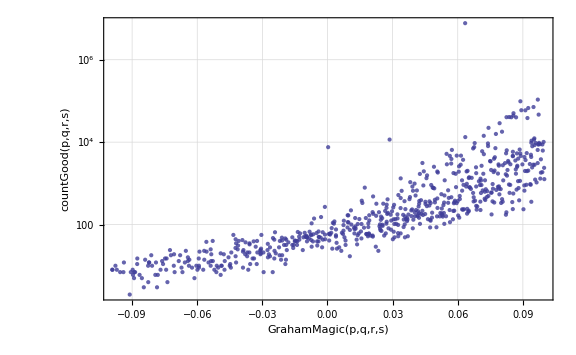

```mathematica
ListLogPlot[Select[gr2500, -0.1<#[[1]]<0.1&], 
			PlotRange->All,
			LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
                              Ticks->{All,All,All},
			GridLines->{Automatic,{1,100,10^4, 10^6}},  
                              PerformanceGoal->"Quality", 
                              Method->"QuasiNewton",
                              ImageSize->Large,
                              PlotStyle->Opacity[0.8],
                             Frame->True,
			 AxesLabel->{"GrahamMagic(p,q,r,s)","countGood(p,q,r,s)"}
                               ]
```

```mathematica
Sort[formulaValues]
```

{{0.293221,3,{3,5,7,11,3}},{0.296593,5,{3,5,7,13,5}},{0.301639,2,{3,5,7,17,2}},{0.303602,3,{3,5,7,19,3}},{0.307098,4,{3,5,11,13,4}},{0.312323,10,{3,5,11,17,10}},{0.314355,3,{3,5,11,19,3}},{0.315914,4,{3,5,13,17,4}},{0.31639,4,{3,7,11,13,4}},{0.31797,8,{3,5,13,19,8}},{0.321773,9,{3,7,11,17,9}},{0.32338,2,{3,5,17,19,2}},{0.323867,7,{3,7,11,19,7}},{0.325472,5,{3,7,13,17,5}},{0.327591,12,{3,7,13,19,12}},{0.333164,8,{3,7,17,19,8}},{0.33317,8,{5,7,11,13,8}},{0.337001,11,{3,11,13,17,11}},{0.338838,12,{5,7,11,17,12}},{0.339194,18,{3,11,13,19,18}},{0.341043,11,{5,7,11,19,11}},{0.342734,10,{5,7,13,17,10}},{0.344965,16,{5,7,13,19,16}},{0.344965,13,{3,11,17,19,13}},{0.348931,40,{3,13,17,19,40}},{0.350833,8,{5,7,17,19,8}},{0.354874,21,{5,11,13,17,21}},{0.357183,21,{5,11,13,19,21}},{0.36326,61,{5,11,17,19,61}},{0.365611,102,{7,11,13,17,102}},{0.367437,268,{5,13,17,19,268}},{0.367991,55,{7,11,13,19,55}},{0.374251,596,{7,11,17,19,596}},{0.378554,6620,{7,13,17,19,6620}},{0.391963,244453,{11,13,17,19,244453}}}

Filling::invfillentry: 3 → {2} is not a valid Filling specification.

Filling::invfillentry: 4 → {3} is not a valid Filling specification.

Filling::invfillentry: 5 → {4} is not a valid Filling specification.

General::stop: Further output of Filling will be suppressed during this calculation.

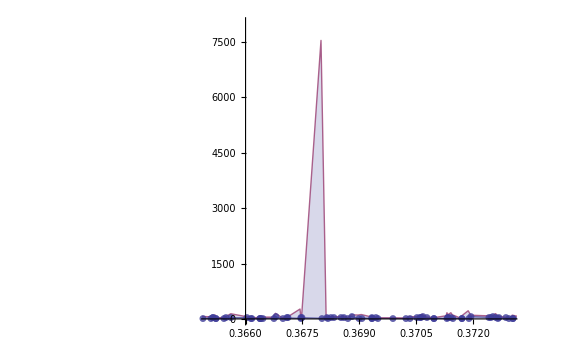

```mathematica
ListPlot[{formulaTable[myData[10]],formulaTable[myData[2500]]}, 
			PlotRange->{{0.365,0.373},{0,8000}}, 
			GridLines->{Join[Table[n,{n,0,0.6,0.01}],{{1/E,{Red, Thick}}}],Automatic},
			LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
                              Ticks->{All,All,All},  
                              PerformanceGoal->"Quality", 
                              Method->"QuasiNewton",
                              ImageSize->Large,
                              PlotStyle->Opacity[0.8],
                              Joined->True,
                             Filling->Join[{{1->Axis}},Table[{i+1->{i}},{i,1,7}]],
                             PlotMarkers->Automatic,
			 AxesLabel->{"formula(p,q,r,s)","countGood(p,q,r,s)"}
                               ]
```

```mathematica
myFormula[7,11,13,19]
```

0.367991

```mathematica
formulaInvValues = Table[{myFormulaInv[x[[1]]  ,x[[2]],x[[3]],x[[4]]], x[[5]] },{x,huge}]
```

{{5.27622,3},{5.13967,5},{4.96634,2},{4.90712,3},{4.653,4},{4.49608,10},{4.44247,3},{4.37972,4},{4.3275,8},{4.18156,2},{4.13043,4},{3.99113,9},{3.94354,7},{3.88784,5},{3.84149,12},{3.71193,8},{3.51971,11},{3.47774,18},{3.36045,13},{3.27349,40},{3.9224,8},{3.79012,12},{3.74493,11},{3.69204,10},{3.64801,16},{3.52499,8},{3.34244,21},{3.30258,21},{3.19121,61},{3.10862,268},{3.24428,102},{3.20559,55},{3.09749,596},{3.01732,6620},{2.91411,244453}}

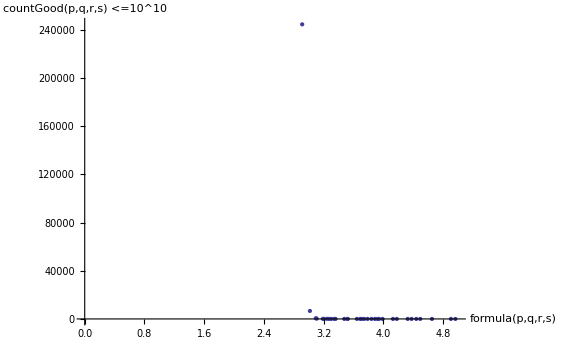

```mathematica
ListPlot[formulaInvValues, 
			PlotRange->{{0,5},All}, 
			GridLines->{Join[Table[n,{n,0,10,0.5}],{{E,{Red,Thick}}}],Automatic},
			LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
                              Ticks->{All,All,All},  
                              PerformanceGoal->"Quality", 
                              Method->"QuasiNewton",
                              ImageSize->Large,
                              Mesh->None,
                               ColorFunction->"DarkRainbow",
			 AxesLabel->{"formula(p,q,r,s)","countGood(p,q,r,s) <=10^10"}
                               ]
```

```mathematica
Join[Table[n,{n,1,10,0.5}],{{E,{Red,Thick}}}]
```

{1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,{ⅇ,{RGBColor[1,0,0],Thickness[Large]}}}

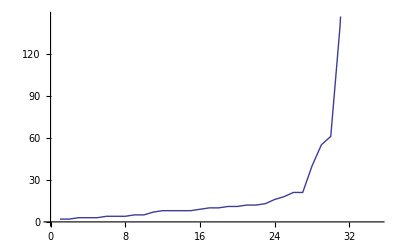

```mathematica
ListLinePlot[Sort[ Table[x[[5]] ,{x,huge}]]]
```

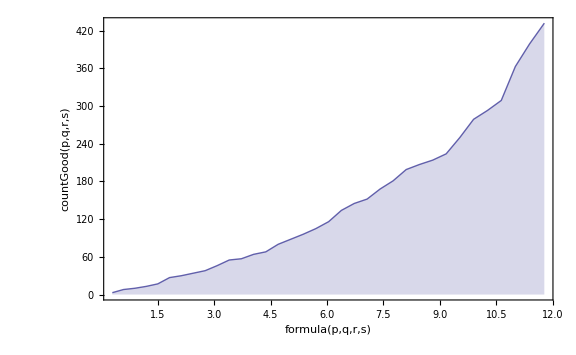

```mathematica
ListPlot[Accumulate[formulaTable[myData[10]]], 
                             PlotRange->All,
			LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
                              Ticks->{All,All,All},  
                              PerformanceGoal->"Quality", 
                              Method->"QuasiNewton",
                              ImageSize->Large,
                              PlotStyle->Opacity[0.8],
                              Joined->True,
                             Filling->Axis,
                             Frame->True,
			 AxesLabel->{"formula(p,q,r,s)","countGood(p,q,r,s)"}
                               ]
```